```mathematica
kappa0=1;
nu=0.8;
omega=0.5;
kappaMax=3;
X1=List[-1.0,-2.0];
X2=List[5.0,2.4];

GoldenRat[precision_,newF_[kp___], lla_, rrb_]:=Module[{},
eps = 10^-precision;
leftBound = lla;
rightBound = rrb;
intervals=List[];
(*goldenRat = (1+Sqrt[5])/2;*)
goldenRat=GoldenRatio;
nextLeftBound[a_, b_]:= a+(1-1/goldenRat)(b-a);
nextRightBound[a_, b_]:= a +(b-a)/goldenRat;
(*nextLeftBound[a_, b_]:= a+(b-a)/(goldenRat+1);
nextRightBound[a_, b_]:= b-(b-a)/(goldenRat+1);*)
AppendTo[intervals, {leftBound,rightBound}];
nextLeft=nextLeftBound[leftBound, rightBound];

nextRight=nextRightBound[leftBound, rightBound];
leftFunc = newF[leftBound];
rightFunc = newF[rightBound];
IterationCountrer=1;

While[(rightBound-leftBound) > eps,
If[leftFunc > rightFunc,
leftBound = nextLeft;
nextLeft=nextRight;
leftFunc=rightFunc;
nextRight = leftBound + rightBound  - nextLeft;
(*nextRight= nextRightBound[leftBound, rightBound];*)
rightFunc=newF[nextRight];
,
rightBound = nextRight;
nextRight=nextLeft;
rightFunc=leftFunc;
nextLeft = leftBound + rightBound  - nextRight;
(*extLeft= nextLeftBound[leftBound, rightBound];*)
leftFunc=newF[nextLeft];
];
AppendTo[intervals, {leftBound,rightBound}];
++IterationCountrer;
];
(*Subscript[x, min]=SetPrecision[(rightBound+leftBound)/2,20];
Subscript[y, min]=SetPrecision[F[Subscript[x, min]],20];
*)
Return[(rightBound+leftBound)/2];
];
```

```mathematica
(*F[x_, y_]:=5 x^2+4x y+2 y^2+4 √5(x+y)+51;*)
(*
 {N[(-4*5^(1/2)-10 x-4 y), precision],N[(-4*5^(1/2)-4 x-4 y), precision]};
128;8;*)
alpha=128;
F[x_, y_]:=alpha(x^2-y^2)+(x-1)^2;
(*128: {N[-2+258 x, precision],N[-256 y, precision]};
8: {N[-2+18 x, precision],N[-16 y, precision]};

Grad[alpha(x^2-y^2)+(x)^2-2x+1, {x, y}]*)
(*наискорейший спуск*)
```

```mathematica
FastDescent[initX_, initY_, precision_ ]:=Module[{},
Dir[x_, y_] := -{N[-2+258 x, precision],N[-256 y, precision]};
eps=10^-precision;
currDir = Dir[initX, initY];
kappa=kappa0;
XY ={initX, initY};
it=0;
While[ Norm[currDir] > eps,
++it;
infunc=XY+kp*currDir;
FF[kp_]:=F[infunc[[1]], infunc[[2]]];
kappa=GoldenRat[precision, FF[kp], 0, kappaMax];
XY+=Abs[kappa]*currDir;
currDir=Dir[XY[[1]], XY[[2]]];
];
Print["x_min: ", NumberForm[XY[[1]],{25, precision}]];
Print["y_min: ", NumberForm[XY[[2]],{25, precision}]];
Print["iterations: ", it];
	Return[XY];
];
```

```mathematica
resFast=FastDescent[X2[[1]], X2[[2]], 6];
F[resFast[[1]], resFast[[2]]]
```

x_min: 2.000000×10^5102

y_min: 1.129570×10^5101

iterations: 2066

0``-10206.632837393454

```mathematica
GradientDescent[initX_, initY_, precision_ ]:=Module[{},
Dir[x_, y_] := -{N[-2+258 x, precision],N[-256 y, precision]};
eps=10^-precision;
currDir = Dir[initX, initY];
(*normDir = Norm[currDir];kappa =Abs[ betha/normDir];*)
κArray=List[];
kappa=kappa0;
AppendTo[κArray, kappa];
points=List[];
XY ={initX, initY};
fValues=List[];
Fcurr=F[initX, initY];
AppendTo[fValues, Fcurr];
AppendTo[points, XY];
norm=List[];
AppendTo[norm, Norm[currDir]];
(*
infunc=xx+kp*currDir;
FF[kp_]:=F[infunc[[1]], infunc[[2]]];
Dexot[2, FF[kp], 0, kappaMax]
*)
it=0;
While[ Norm[currDir] > eps,
++it;
Xcurr=XY+Abs[kappa]*currDir;
While[Fcurr-F[Xcurr[[1]], Xcurr[[2]]]<=omega*kappa*(Norm[currDir])^2,
kappa=kappa*nu;
Xcurr=XY+kappa*currDir;
];
XY=Xcurr;
Fcurr=F[XY[[1]], XY[[2]]];
AppendTo[κArray, kappa];
AppendTo[points, XY];
AppendTo[fValues, Fcurr];
currDir=Dir[XY[[1]], XY[[2]]];
AppendTo[norm, Norm[currDir]];
];
Print["x_min: ", NumberForm[XY[[1]],{25, precision}]];
Print["y_min: ", NumberForm[XY[[2]],{25, precision}]];
Print["iterations: ", it];
	Return[XY];
];
```

```mathematica
gradOut =GradientDescent[X2[[1]], X2[[2]], 2];
F[gradOut[[1]], gradOut[[2]]]
```

x_min: -0.00×10^1528

y_min: -1.60×10^1528

iterations: 634

-3.×10^3058

iterations: 96

```mathematica
ContourPlot[F[{x,y}],{x,-3,3},{y,-3,3},Contours->fValues,ColorFunction->(If[#<0,Darker[Blue,Abs[0.5#]],Lighter[Orange,0.5#]]&),ColorFunctionScaling->True,ContourStyle->Black,FrameLabel->Automatic,PlotLabel->Style[Row[{Style["F(x,y)",Italic]," = ",F[{x,y}]}],Large],LabelStyle->Large,FrameStyle->Thick,ImageSize->350,PlotPoints->100,
Epilog->{Purple,Thickness[0.01],Arrowheads[.08],Table[Arrow[points[[i-1;;i]]],{i,2,Length[points]}],Darker[Red],PointSize[0.035],Point[points[[1;;-1]]],Black,Point[points[[-1]]]}];
```

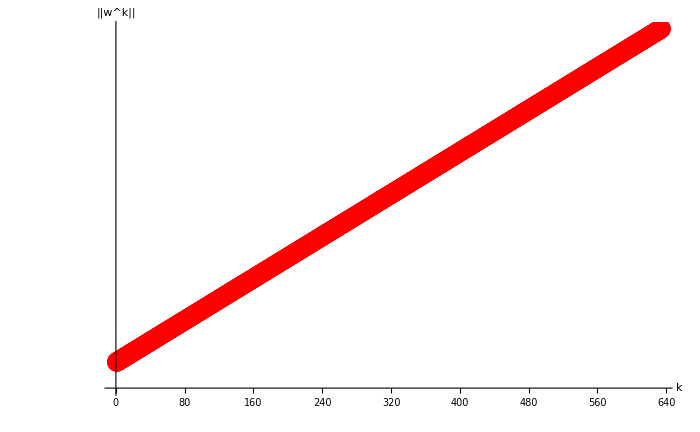

```mathematica
ListLogPlot[norm,PlotRange->All,PlotStyle->{Blue,Thick,PointSize[Large]},AxesStyle->Thick,LabelStyle->Large,AxesLabel->{"k","||w^k||"},ImageSize->700,Joined->True,Mesh->Full,
MeshStyle->Directive[PointSize[0.02],Red]]
```

```mathematica
(*"шапка" таблицы*)
gridLabel={"k","(X^k)","f(X^k)","κ_k","||w^k||"};
gridData=Table[Table[{},{j,1,Length[gridLabel]}],{i,1,Length[points]}];
(*в 1-м столбце-номер итерации*)
gridData[[All,1]]=Table[i,{i,0,Length[points]-1}];
(*во 2-м столбце-точки траектории*)
For[i=1,i<=Length[points],i++,gridData[[i,2]]="( "<>ToString[SetAccuracy[points[[i,1]],6]]<>", "<>ToString[SetAccuracy[points[[i,2]],6]]<>" )"]
(*в 3-м столбце-значение функции*)
gridData[[All,3]]=SetAccuracy[fValues,6];
(*в 4-м столбце-значение шага спуска*)
gridData[[All,4]]=SetAccuracy[κArray,6];
(*в 5-м столбце-значение нормы невязки*)gridData[[All,5]]=SetAccuracy[norm,6];
gridData={gridLabel}~Join~gridData;
(*выводим всю таблицу*)
table=Grid[gridData,Frame->All,FrameStyle->Thick,Spacings->{2,2},ItemStyle->Directive[FontSize->15]]
```

1
 |  |  |  |

```mathematica
{{"k", "(X^k)", "f(X^k)", "κ_k", "||w^k||"}, {0, "( -1.00000, -2.00000 )", -380.`8.579783596616812, 1.`6., 574.2334020239505889549`8.759088450948324}, {1, "( 259.00000, -514.00000 )", -2.5164156`13.400782368840469*^7, 1.`6., 147577.9843201553157996386`11.169021574279618}, {2, "( -665LinguisticAssistant61.00000, -132098.00000 )", -1.66206740518`18.22064863262747*^12, 1.`6., 3.79275419702799096703529358`13.578954697610914*^7}, {3, "(                  7\n1.710617900000 10,                   7\n-3.394918600000 10 )", -1.09777890044799344`23.040514879290317*^17, 1.`6., 9.7473782863619365692138671875`15.98888782094221*^9}, {4, "(                     9\n-4.39628800100000 10,                     9\n-8.72494080200000 10 )", -7.250719859568954834944`27.860381125952905*^21, 1.`6., 2.50507621959501806640625`18.398820944273503*^12}, {5, "(                       12\n1.12984601625900000 10,                        12\n-2.24230978611400000 10 )", -4.78902796004669842767478784`32.68024737261549*^26, 1.`6., 6.43804588435919625`20.8087540676048*^14}, {6, "(                          14\n-2.9037042617856100000 10,                          14\n-5.7627361503129800000 10 )", -3.163105077331243197906492063744`37.50011361927808*^31, 1.`6., 1.65457779228031328`23.218687190936095*^17}, {7, "(                           16\n7.462519952789017600000 10,                             17\n-1.4810231906304358400000 10 )", -2.089199272526512674854919334772342784`42.319979865940674*^36, 1.`6., 4.2522649261604052992`25.628620314267387*^19}, {8, "(                               19\n-1.917867627866777600000000 10,                               19\n-3.806229599920219750400000 10 )", -1.37989522751103599459535961558498907521024`47.139846112603266*^41, 1.`6., 1.0928320860232240594944`28.038553437598683*^22}, {9, "(                                21\n4.92891980361761921433600000 10,                                 21\n-9.78201007179496528281600000 10 )", -9.11406998818764245549955033212352402802343936`51.95971235926586*^45, 1.`6., 2.808578461079685799346176`30.44848656092998*^24}, {10, "(                                    24\n-1.26673238952972799862374400000 10,                                    24\n-2.51397658845130593927168000000 10 )", -6.01975208649805642442382732950156807919549806542848`56.77957860592845*^50, 1.`6., 7.21804664497479208019165184`32.85841968426127*^26}, {11, "(                                     26\n3.2555022410914008329827123200000 10,                                      26\n-6.4609198323198560545485619200000 10 )", -3.9759860556110999381775865675164377687755798322207522816`61.599444852591034*^55, 1.`6., 1.8550379877585217034225975296`35.268352807592564*^29}, {12, "(                                        28\n-8.366640759604900546210483404800000 10,                                         29\n-1.6604563969062030225116548300800000 10 )", -2.62609902987057595544598532893216984201332381596055750311936`66.41931109925362*^60, 1.`6., 4.7674476285394005068764105670656`37.67828593092386*^31}, {13, "(                                          31\n2.150226675218459737684038385664000000 10,                                           31\n-4.267372940048941820631511046553600000 10 )", -1.73451214823921637185731753937965287293744500541389549476096507904`71.23917734591622*^65, 1.`6., 1.2252340405346258987420401241423872`40.088219054255156*^34}, {14, "(                                             33\n-5.52608255531144141325798796689408000000 10,                                              34\n-1.096714845592578124463492004262707200000 10 )", -1.1456279287905202070961620445252086526204411383113041769412946561073152`76.0590435925788*^70, 1.`6., 3.148851484173989279190061993718448128`42.49815217758645*^36}, {15, "(                                               36\n1.42020321671504041323134378771375718400000 10,                                                36\n-2.81855715317292605887817856581212569600000 10 )", -7.56675790686850991456009027721257422238829705079982800424733440688676405248`80.87890983924139*^74, 1.`6., 8.0925483143271533447680910690890022912`44.90808530091775*^38}, {16, "(                                                  38\n-3.6499222669576538324897630164890733772800000 10,                                                  38\n-7.2436918836544193810211085554315113267200000 10 )", -4.9977679299075815489002422651297559041432769642466948011465913429538034715459584`85.69877608590397*^79, 1.`6., 2.07978491678207789430076879402018787033088`47.31801842424904*^41}, {17, "(                                                   40\n9.380300226081170258829254481279730476646400000 10,                                                     41\n-1.8616288140991856630521574863195538771148800000 10 )", -3.300975740024657589475152142515150789214302862923243795312901058865830921749747728384`90.51864233256657*^84, 1.`6., 5.3450472361299404127296079211070576522166272`49.72795154758034*^43}, {18, "(                                                       43\n-2.410737158102860454771233825877448725836595200000 10,                                                       43\n-4.784386052234906887113223768931131689061580800000 10 )", -2.18026146652888600092426996765460786488005393831198698087341963155232616683207220994768896`95.33850857922916*^89, 1.`6., 1.3736771396853945187020159243411006502580781056`52.13788467091163*^46}, {19, "(                                                        45\n6.19559449632435071017797003268273697906596249600000 10,                                                          46\n-1.229587215424371055132818037190737545299335577600000 10 )", -1.4400408960276640498054337472922446870945545065031869612246300353813080784134988308341365669888`100.15837482589173*^94, 1.`6., 3.530350248991464255329842987178567075273126182912`54.547817794242924*^48}, {20, "(                                                            48\n-1.59226778555535816040405150342051023654742287974400000 10,                                                            48\n-3.16003914364063353309700514142997259862369370112000000 10 )", -9.5113261141731163600036398639263498946215020485530477602673031250335838866985332007105823720341504`104.97824107255434*^98, 1.`6., 9.07300013990806274677543208693684524366470959857664`56.957750917574224*^50}, {21, "(                                                             50\n4.0921282088772710012036548270262759644711903402393600000 10,                                                              50\n-8.1213005991564289394327187741935702510479809603174400000 10 )", -6.2821357851502028079348513901455243590225432450071095305685018359438418318279244483865371247449298960384`109.79810731921691*^103, 1.`6., 2.33176103595637233693623037719816405110120118633889792`59.367684040905516*^53}, {22, "(                                                                 53\n-1.0516769496814586406631993116211735583500606160397926400000 10,                                                                 53\n-2.0871742539832022025419738356137058907943957744425369600000 10 )", -4.14928786473385697215090059212798154414463118224371943615490431690810766314153959834100647970233477805113344`114.6179735658795*^108, 1.`6., 5.9926258624078763572207954093860092766385325651647266816`61.77761716423681*^55}, {23, "(                                                                  55\n2.702809760681348759673542062263050961111938194436050124800000 10,                                                                   55\n-5.364037832736829384053449634264722575349728602005648179200000 10 )", -2.74056314177806498962363865479549558806853900918200892494133263233508866817370701941439013320481224516468784234496`119.4378398125421*^113, 1.`6., 1.5401048466388241486713978040689916513829895483129136676864`64.18755028756811*^58}, {24, "(                                                                     57\n-6.94622108495106618713709207311068641553582562480994700492800000 10,                                                                      58\n-1.378557723013365288903586898528422170297521967204394441113600000 10 )", -1.8101145495129949020825972654281933973185469343704191413838203488945517833353097589056012478931810397075802454686171136`124.25770605920468*^118, 1.`6., 3.9580694558617788314612017057638069270365635455326600822784`66.5974834108994*^60}, {25, "(                                                                       60\n1.78517881883242394319199706719757698418555236763107186232524800000 10,                                                                        60\n-3.54289334814434846912141295052400942539671650231405187694592000000 10 )", -1.195562558807837341990574103953623439389318452790328104782419342218854945365554743071565555348516669490175981689912051105792`129.07757230586728*^123, 1.`6., 1.017223850156476980565943403783333307433507665290254025110847488`69.00741653423069*^63}, {26, "(                                                                          62\n-4.5879095643993288881738515132509266704824684089153054729830400000000 10,                                                                          62\n-9.1052359047309753016012081322441262274866570627905130929428889600000 10 )", -7.8965711446698876174346405959645251161415133630859084461185960751649362317318382184754655787344271016431205138413007053858537472`133.89743855252988*^127, 1.`6., 2.61426529490214595880148258085902870415350735799394819157939716096`71.41734965756199*^65}, {27, "(                                                                            65\n1.1790927580506273899852169091287825443504503752827310756678388940800000 10,                                                                             65\n-2.3400456275158604332862648903513027099113459576947089164964410163200000 10 )", -5.215606275343012571286459245364625904078353408374289917502068568706338638923335744366873891955915740297940610314489271378060228165632`138.71730479919245*^132, 1.`6., 6.7186618078985141319907099464409427367983063247022576435723818237952`73.82728278089328*^67}, {28, "(                                                                               67\n-3.030268388190111971349535905160930696319425642187109203557773580697600000 10,                                                                               67\n-6.013917262715761842024692827057343186924594621483341822981060952064000000 10 )", -3.44485578880130756564609171068770817710172264777937103170891951717802968054213870411068296755578651635943560114057762621416825683280134144`143.53717104585505*^137, 1.`6., 1.7266960846299182516478265863828893426030262215663851846120960493092864`76.23721590422457*^70}, {29, "(                                                                                69\n7.78778975764858680855859423508305541557403193147763089143152673764147200000 10,                                                                                  70\n-1.545576736517950698816636893737159222235390235788073922037077467411251200000 10 )", -2.275292799945375259107431214992753370828250899495291896055853250171769791171654842857890421176487759611368054182319873966245201813186503770112`148.35703729251765*^142, 1.`6., 4.43760893749888912822717956713248556444948759706854464613361277745496064`78.64714902755587*^72}, {30, "(                                                                                    72\n-2.00146196771568673164228613425601346552682782172398277454220714021014732800000 10,                                                                                    72\n-3.97213221285113335419358736980827581876213993768709895714737573422379827200000 10 )", -1.502808141435921025620844773613428687318185476408386801972114843217949563625374529840213409268249909847098026905200422095590982367099233838137606144`153.17690353918022*^147, 1.`6., 1.140465496937214709175553831896838519247200888794816195370095998329042239488`81.05708215088715*^75}, {31, "(                                                                                     74\n5.1437572570293155162612831498560045577907846540829028106171003383734652108800000 10,                                                                                       75\n-1.02083797870274135441471223099091191076660614358620614333029077228596913766400000 10 )", -9.9258974933701169018268806648469986326778642991699307985390163031217061373607392283551236672304081431110992449959824116922717464607152699707955519422464`157.99676978584282*^151, 1.`6., 2.9309963271286420175091367676148243482027361348331757094457971341541802770432`83.46701527421845*^77}, {32, "(                                                                                         77\n-1.3219456150565340635750791056281390382228002709818669844955498802200880296755200000 10,                                                                                         77\n-2.6235536052660452065249258866683433668544310182377794217069588223207720511078400000 10 )", -6.555956035396028805490862948369843845140816026771135481766940198320512147339723746635585455241983125697586304059764971953216275737859477229479362629474451456`162.81663603250541*^156, 1.`6., 7.5326605607206092805168428896287617772848505841555766275419061603998643158777856`85.87694839754974*^79}, {33, "(                                                                                          79\n3.397400230695292491965935885176628510889809741506194869443067391116255506622054400000 10,                                                                                           79\n-6.742532765533736345319515260858246668312805972606143612060470736722370506208051200000 10 )", -4.33014340181872308362621829042806028787034053241601580851230453675152583740159329815935021772826061443408477379366770224362641791801029033311229814718846914789376`167.636502279168*^161, 1.`6., 1.9358937641051968022994301890337893412181386976982498509994041468553070911969820672`88.28688152088104*^82}, {34, "(                                                                                             81\n-8.73131859288690178991869220560664946504520852865314707357094820811492954614634905600000 10,                                                                                              82\n-1.732830920742170118321576357342839857426683952692901337583992576199307386958957772800000 10 )", -2.8600164154672476259653739800528018130354187624413878028229492426843122500624800960745651606746147029995067423661011681537559936567812722912063133462243451346184306688`172.45636852583058*^166, 1.`6., 4.975246973750355512310068914310440660260465582888195380697024432012414413340141420544`90.69681464421234*^84}, {35, "(                                                                                               84\n2.24394887837193366901928389520749960551544267317260527438237126341110476963492711628800000 10,                                                                                                84\n-4.45337546630737686708711789898810100024888917067537301712655563907506397068939336089600000 10 )", -1.8890122422519619546384023560268938343197982685792123540148293952936377614138113512167684694833511143521818447662594767566420300921994181732824663487449850992885124562944`177.27623477249318*^171, 1.`6., 1.27863847225384125537302786897994217730150137558523079206500310277970730223271323631616`93.10674776754362*^87}, {36, "(                                                                                                  86\n-5.7669486174158702066134198895073456282101066559867180769277620411857199832844521491660800000 10,                                                                                                   87\n-1.14451749484099586950760028696989000536282072420224995186013136510436287018753806932377600000 10 )", -1.2476736958849984695043643727226442839982365226124119816395253224188217613231586065114835720728015116079399054652185901546430758756167407884525329000584060404595031186417385472`182.09610101915578*^176, 1.`6., 3.28610087369237199538885798965672562795715227225296910862608977882051599960996449471168512`95.51668089087492*^89}, {37, "(                                                                                                    89\n1.4821057946758785801557222288734460850450239466221144194163210183908046526218832812861030400000 10,                                                                                                     89\n-2.9414099617413592631637970339986946549307460851241344131410196981194092055215464992944947200000 10 )", -8.240759993950824568086738323589301563498070966968127670513047020676440755717454062693754255381982456012285244437676382892733526153707520945280393056801076145514649932529777548197888`186.91596726581835*^180, 1.`6., 8.4452792453893955136434997699522680891936491233522588002057399613884855139858829349981519872`97.92661401420622*^91}, {38, "(                                                                                                       91\n-3.809011892317007996231490986531395275898127561837548063083532777280213285151358785996351078400000 10,                                                                                                       91\n-7.559423601675293560756935705463988723166857545749291720930101774256011627701667489324099174400000 10 )", -5.44293956840458062667306470871803390103748865082334609457029008143926908420114436896230525822559043526646348700526540799910281899675588809498504924689299698110524389381065868386630631424`191.73583351248095*^185, 1.`6., 2.1704367660650745037136690096989410622536738764502445432312691463466427782656117045020271312896`100.33654713753751*^94}, {39, "(                                                                                                        93\n9.78916056325470947200110081287861597705338994051635663854794703883239552539024100631960249958400000 10,                                                                                                          94\n-1.942771865630550472615153670166841514951991328820946087430657514073428947690504746635661777305600000 10 )", -3.5950071555355420432022734942740875981725271660851957888603286134440816341294309140159111426448685013688827290351860528463188880885969211809295844589886866555265757023390273068297520217587712`196.55569975914355*^190, 1.`6., 5.578022488787242293425784441226412565485947843918012814429693261520940827186656184531862541041664`102.74648026086881*^96}, {40, "(                                                                                                            96\n-2.51581426475646060479460336728043681556454219500765640134550656791628324619820818110920868128358400000 10,                                                                                                            96\n-4.99292369467051517408395502599944613415628622954344980647208896443047050413229054225294917894144000000 10 )", -2.374466276159670202175850442126202655219584422599077746710651496380969099221483400422137327799485171574783680213019743403671622800409031124895043638714767848594490701958039970238765865270463430656`201.37556600580612*^195, 1.`6., 1.433551779618321247593344315657019752402337884489988447226713737449549278528530490989728438809526272`105.1564133842001*^99}, {41, "(                                                                                                             98\n6.4656426604241043898632233254138854656295245992544755112297205147662733522578689146429861778371379200000 10,                                                                                                               99\n-1.28318138953032245570513534857541975816188260327177572716860201233335345562495383273564506159893708800000 10 )", -1.56831123074070062237622708749042982642711109504080768025651331555754772229190384677696872664750318412186072911962162475094132906908577320925486747145014026638031064324434352834819683178287438980186112`206.19543225246872*^200, 1.`6., 3.68422807361908574473005346232173706668566922431499240764414158771028253500995755574053240861158801408`107.56634650753139*^101}, {42, "(                                                                                                                 101\n-1.6616701637289948366940247981189332499394336643612954229465680931480426570069516036709536954769316249600000 10,                                                                                                                 101\n-3.2977761710929284343318807036724361724527165680570194222803326067668366025728629623367471665670573260800000 10 )", -1.0358538847919253550930591752247468255408519637442428292054432658285059876395123171024949091962456841398397973254591154160167510504337442964461797445113010442078097359883041727708565654282256862611492569088`211.01529849913132*^205, 1.`6., 9.4684661492010496428375446039762331360779100935993123419840252242612358263028244231718976219583866732544`109.97627963086269*^103}, {43, "(                                                                                                                  103\n4.270492320783516680571320090186994236806119702726445226927064919655697884461467932118401296122376722841600000 10,                                                                                                                   103\n-8.475284759708825485661590171816523403687061905556792295968775727540355608061285252578537515693953882521600000 10 )", -6.84171132366218665479869529854102521944669214625677978235811666292380847335468163985985979116119909312016613843242976668021334455968336628543827877626790531418717400063802885300202582269963850131002556906733568`215.8351647457939*^209, 1.`6., 2.43339580034466983937240114529907191573040579161618437628433829276228509364354690571880760128875226202112`112.38621275419399*^106}, {44, "(                                                                                                                      106\n-1.097516526441363891941496792924996342075903572209257852536594732751352279732589178389714902150499730351718400000 10,                                                                                                                      106\n-2.178148183245168148223594317645529259850351715658268931742515679426358695462265583854573751093239346102272000000 10 )", -4.5188819121656377840180233230537514205206690896158677266723117411637468587453024846227924856328723222237610675669781368336044631285756111864741179728151463284601113314554219053623419069140675245570766737628677013504`220.6550309924565*^214, 1.`6., 6.25382720688580069274304017296904117873332440479611103697807588268393494256914029948862862761077790186930176`114.79614587752528*^108}, {45, "(                                                                                                                       108\n2.82061747295430554654872675834538917850239352176270189871720699271420171642049012935200695853068765199807283200000 10,                                                                                                                        108\n-5.59784083094008208797170201165237195483581601059791896724008706081139933079837086729234074646287075871450726400000 10 )", -2.98467631416628129898907480070215621281899232751707155805231623929572516911370829755283081536422866995077555920099225823789041251722491606069955838200413940145076201725190277801995436672147195870503155500353625199214592`225.4748972391191*^219, 1.`6., 1.607233592169650936565249146708088760689981626804046542172841770507594049747263387523947830077885742797127942144`117.20607900085658*^111}, {46, "(                                                                                                                          110\n-7.2489869054925653432820334590244846631539077105062814486631264636170440388854919883373320491242807187365009817600000 10,                                                                                                                           111\n-1.43864509355160105176134336201461391710670443870279558087157421967927713400991317990807287625133686165595173683200000 10 )", -1.97134885874368701371461133463952311061388577872385299338935688396069360894148016959465748100278440886469357332803679185685123326951759220225179331548708825701785172329911738841451060288975291724918194331762238571079335411712`230.29476348578166*^224, 1.`6., 4.13059033187600295236241482035912736586746403698938204869167445028338806922510107215871509613877804697656315871232`119.61601212418788*^113}, {47, "(                                                                                                                            113\n1.8629896347115890555949248527680458919843894702374415827555453889719596613851925707807498435286789546607485806182400000 10,                                                                                                                             113\n-3.6973178904276148819155666987537771675472982991661742408164494919454117174702115274746493260945817988788707445964800000 10 )", -1.3020562077116180944254077789997651735480873055016465008810365826230183404191831888643606061107366063192905133827838313582775321198686474653969072043073755372451785214507951329604919502260906752087105099878271924427269200674816`235.11462973244426*^229, 1.`6., 1.0615617152921328120713770254182113896076800434982919669972652117448838716690095067873941351924540866461104217260032`122.02594524751916*^116}, {48, "(                                                                                                                               115\n-4.787883361208783719087890285308352009958318094302472616287026039978936893572949143706706841662585311824853592755404800000 10,                                                                                                                               115\n-9.502106978398970738654419491974890304409557730321875003361397145272506309696830067849273587922657948409162643800064000000 10 )", -8.59995104631446803772625822914005553052068958118258505023681618765650994166577825382455987947676950694610486924715484879020612752828244785541232328527830523743520415262877886468409032717980844726432245911753938448442267034580800241664`239.93449597910686*^233, 1.`6., 2.7282136083007811660417856112951256374755737959336778651897014804439162292526378006710621863705390534299339549390667776`124.43587837085046*^118}, {49, "(                                                                                                                                 118\n1.230486023830657389558579105928103374089261024824279078147732521556037544539000653013187667914773346456829249061493145600000 10,                                                                                                                                  118\n-2.442041493448535679311451909648234311005459449819790396072931163796008323622364632024976839079207290725556543959125196800000 10 )", -5.68018166658024376161065931499704099520614233979157069312350238360422350549749080460195644613203136919083569952414442047573385935173851915318739689291098801352138191668825633540845525391179651968564118955548905584435831741975820696027136`244.75436222576943*^238, 1.`6., 7.011508973333008613571501969751584481391020033623254380764588549271753553774330985286139334765354570233312209503032180736`126.84581149418176*^120}, {50, "(                                                                                                                                    120\n-3.16234908124478915744358171774239829835050102910019979071449349243623578936685563463890350069698663864330467261857713356800000 10,                                                                                                                                    120\n-6.27604663816273648977391512743797480799934097373998773071604734536798418091047981563533832785875576212395093698709710438400000 10 )", -3.751703188959585244974123685026386569891860578294531656133303767977445654474549929994725314570737719144042276127990570778925573905309226956166890579334796298449545077493447246665574781039341065168715740144506151751066820312761010132243670106112`249.57422847243203*^243, 1.`6., 1.8019578061465832182748732382063002349391339392453502574496292354994029107951807419923835612116657406899983440625306435584`129.25574461751307*^123}, {51, "(                                                                                                                                     122\n8.1272371387991078766114107157149185705434369233027326225226869941294995581940745499931584368367147534362057837406034958745600000 10,                                                                                                                                       123\n-1.61294398600782325493691002785084440954762167723030743882837427607676069711810491874905318937485215016566985970442709028044800000 10 )", -2.47796243927591651174496182808432715781997364517119741793404000654334288651303526511347685244089252733851886413841291783561213629715247959053163689335004064160307451817262845929056775971937182162920770564426101622474417654987344594346004248052891648`254.39409471909462*^248, 1.`6., 4.63103156179671872124683457035832332583918617854031466644578464232807372315381507174210040125769268276248459721169893565923328`131.66567774084433*^125}, {52, "(                                                                                                                                         125\n-2.0886999446713709708861037451912230010251259521691901584349981928648678107214291702301893553009222553214997168220489167929344000000 10,                                                                                                                                         125\n-4.1452660440401054363918971832400182280101041599747062851933650423524930925727936266758031806481879410079117655727591975498547200000 10 )", -1.6366694115173495136967621381036921281419115889308443953775779138714716826624693135833290450711409753588527249021565549802855671075518672696657800575998132926876273059196763673017210824927564909971907186165176221437354176198406786758312167249243677917184`259.21396096575717*^253, 1.`6., 1.19017511138175658059358547573505496585439121865457518499856232986306454586856917852432128474182888741119831141948524164628348928`134.07561086417564*^128}, {53, "(                                                                                                                                          127\n5.367958857805422692493345859210541328101979137705180116373726722293404957932614285054646328832523911837513955509869769002896588800000 10,                                                                                                                                            128\n-1.0653333733183070287631575657186610884569217906080052781148189916743160897948948710377546060891864271761184907877344814803661619200000 10 )", -1.081003779613094178592244552886184032714536053474173481352839698434603202673904595612188377026764056355417119933923233272347660380218274983795251818089478285598011736887626411905540647792800088648345776985262804824566082609050607924816731662928917666218377216`264.0338272124198*^258, 1.`6., 3.0587500362511141254605281851987883994734722033583491943485927219594258084537209708088463290773019447129089583045013639905398489088`136.48554398750696*^130}, {54, "(                                                                                                                                              130\n-1.379565426455993480942592306863660968787802004538977203054554958472297484640779906742971886659810549833456857637038591018495534694400000 10,                                                                                                                                              130\n-2.737906769428048994659975926797288507000038825828877423013355622237949379770020318916346536189268589965984620159586842549140271923200000 10 )", -7.1399218639665248198912360790119894262714144314064522962564063114383300280909543151335795967857659327199078999631325722643145215820215710606804096383609041971173588024772440461256369304004320046732463140050378625929408520139931011775917498201279267323320597479424`268.85369345908236*^262, 1.`6., 7.860987593165363376312319054200534709670023750400233314000394427558436830129113027939463387285935894313925250751785331968114893520896`138.89547711083821*^132}, {55, "(                                                                                                                                               132\n3.54548314599190359571526722164061169876113204043974393193289226865464371356790832301021847075345728937359713623081549107635693813760000000 10,                                                                                                                                                132\n-7.03642039743008632507195241946175329038514082137020820484661888023053908597249628866437397728998036963559286824113795872005589827584000000 10 )", -4.715846991931249793857099343624351881959109398054801556974209262767519684822505292662820582314891401446627934685993356708654673023094530955601129677548432430454118308516925088509750819003038553127549529398978922758624458147265238474889102417181650624817375606156034048`273.67355970574494*^267, 1.`6., 2.020273811443498584407080929330777648082164283769780076656159806046028031741062722175085173846560897018695933828707709222492455246495744`141.30541023416953*^135}, {56, "(                                                                                                                                                  134\n-9.1118916851991931551147805159682897906898396672619821829174842052407970402699313686370065685716714185011217534432386787800067061317632000000 10,                                                                                                                                                   135\n-1.80836004213953222967373871176348731338150610325299097033488903514054881319702015894195249624040083978032557260907797309447771500052480000000 10 )", -3.11476977970067234583837373568700792436792587643753251332032083245853846449474593237310631876350040810001631831274415066575554593062123575372329251885124333509165283075686690223425849919314566818594881422647225883109843811191906404778344145168319492459860128815728574857216`278.49342595240756*^272, 1.`6., 5.19210369540979139097650911685782018920025289432221838321552087086705656091944895707225464447512494492155877434132941635571629467690336256`143.7153433575008*^137}, {57, "(                                                                                                                                                    137\n2.3417561630961925569413775547793213123899157043884435052943551737971206723529432741686629725755807290913143090304328187796086343615696076800000 10,                                                                                                                                                     137\n-4.6474853082985977140602639753212758608741079452246524489239041429961523725366707641516749245799763999013958239991279762371649887777115340800000 10 )", -2.0572742917944966810176102615696392326577525837319081089876605988244523980126155720008814341800917073375407414154027502449881932425749039455540149734316073481379098087846382120135983695049340400364339295258217079073332382352353008199522986657585602211967557452942483449570131968`283.31329219907013*^277, 1.`6., 1.33437064972031638913360276500808128600425326392273772405740057122353658436792037015358392172088547540781363110500987212239711779452255993856`146.1252764808321*^140}, {58, "(                                                                                                                                                       139\n-6.018313339157214284652168014437224203017247481194001960897336665859018012821258408578324117292923053909253508960897042026393518101003396710400000 10,                                                                                                                                                        140\n-1.1944037242327395951607686609135421737568689060624958838778204369376291535198935104338284356638811068634419527252496626436820864590087087718400000 10 )", -1.35880909698734721283803077736180277542120895425673505305733689825789969284397949013162666101221736268098528559966588828441947461512532441376750047887653050608127514270618133533052127976949315447885250031941555726965803581062896352133433777024916679637429472286433458731894605611008`288.1331584457327*^282, 1.`6., 3.429332569781213075650398003366063055462222188479222074358724772844791085897156308854641507742553232345366090391008229596431144650353300996096`148.5352096041634*^142}, {59, "(                                                                                                                                                         142\n1.546706528163404262597415741366360876650105808957351638256611709581608734129354522472546440180046975829473495144497031663198136598722437867110400000 10,                                                                                                                                                          142\n-3.069617571278140721486351656229484086924831345893002527449888784187108693750355714009165504444640925108147297176291225773009149558306943218483200000 10 )", -8.9747982046917283016404206889985249821843162808369227091126435908957339582809650728056395032188769830718449996224345215309923627376637633395090093752459397143596193212158908369150953297686124334580278665895773860204517775994818729512459962564446002118464865953444685586058092065476050944`292.95302469239533*^286, 1.`6., 8.813384704337717355314480037483822012289761667786424250484529175415092665282916892911545551736684737129890303886100930375336431937805827050569728`150.9451427274947*^144}, {60, "(                                                                                                                                                            144\n-3.97503577737994886552174526587122482985828357284679779879368790670877059844503276310356236143298873538257168580592174909521026406035937004879872000000 10,                                                                                                                                                            144\n-7.88891715818482159465084829688289235464182432149595255452901138408356011076014194523630068653623918252848842259944470205049421636594398055838515200000 10 )", -5.927764466216839374786582290234121683668129156179987942525338831953684785941402492639983386352676467783773440667090879488325580390322394019151099473251421860137141668705298326781220460815877690339679765806385656499655288433285746411896265014300605868416478731939518239711160638106437567905792`297.7728909390579*^291, 1.`6., 2.265039869014793105230209510518375175944363807457410316222313063506553899293588224933106888678770657764736446517886754146470054558887489286373900288`153.35507585082598*^147}, {61, "(                                                                                                                                                              147\n1.02158419478664674475963107437549553855859732835519519339605770161567446181071061491814190685762756035437027298239918752442938844596591311460080025600000 10,                                                                                                                                                               147\n-2.02745170965349903614581055334549409242796730075802796562003583530099536647569367472625565640916292527087087433833458643393736418850115801556451328000000 10 )", -3.91522915229155991865400859550762913451877152636713014407781591040366183307151600044103393627701961964440330773830834664450695827765563379493725780075102337413447748404603868173172750963124244307290921717011027170167454982778441416363701294247829023715035088282360204114936534026355778545078239232`302.5927571857205*^296, 1.`6., 5.8211524633680184117552751555940159518107107461819887074410044630105165212584346759865498415788700976285605406430193768488757913484140092861970382848`155.7650089741573*^149}, {62, "(                                                                                                                                                                 149\n-2.6254713806016824268261715603030727055761329793824907299156234528385137048561699932436348048981686231320288861619053590222954058303495818441951228723200000 10,                                                                                                                                                                 149\n-5.2105508938094929700709013899029403703465155815446715618720636133352553353374795055726015598628492018332103635251510426824735298196160406769529729843200000 10 )", -2.5859697027970525954379935104604355247843599993004189219682962382143251490093240797560148266458767237542156271718772987160903827528897520599340798314841349623335741843781737641863391758173520762034536948514913586344461282668130082910480391154937681615757513437187304356329230171629436373098327275732992`307.4126234323831*^301, 1.`6., 1.49603618308558077815707438883260137213474541462906016285697489081022908890841790949429792651488722713521954194768328434877183077601124364938349266337792`158.1749420974886*^152}, {63, "(                                                                                                                                                                  151\n6.747461448146323973225521715405188831328875736013851367190907402667116524259769229006007969850403985110136246266765315330271994158906787877319271147110400000 10,                                                                                                                                                                    152\n-1.3391115797090395806482193913859876400338642818162777665867094420928612775507513599330689433080741293115222027926111560512048481923837427561136616216985600000 10 )", -1.708007129000425234342941776860637401465986578759595289196743858850499226147895314455014158479479648945374139588516808817745195546165675301464212128612786751028254115076354938985105277574875614483776563451739828960656993358953898849392634885479817564590218771278883739267598130806519294353028160709734694912`312.23248967904567*^306, 1.`6., 3.8448129905299424719400657032729727897053055273078865723015459884143101489523589716078309631852256683278892971831585020821398023915015798768256895087017984`160.5848752208199*^154}, {64, "(                                                                                                                                                                      154\n-1.734097592173605228556584232415944833041814470772956662324930243693599846123999768561903940771326859159945943313950948917718934538114273062120899722870784000000 10,                                                                                                                                                                      154\n-3.441516759852231457115157212824594562493706086723779727919474887445025092617806333930774880534188082936116760796061954485428577888524508729789436249138790400000 10 )", -1.12812162863349053473649770854645673597882167858223117858432938781532285290671642026151604653757521819747818959817697347766091672775087778807071387313980055049624039299882178752700089643292102370162219932568357350517161058512878849074503641129981977950210369244253166160340653731672809632025522999790275288629248`317.05235592570824*^311, 1.`6., 9.881169385661951063255871071792608598991539143189702878034478294881529464655471318165265750219120784069928490932060729851815701414706137716113474922502684672`162.99480834415118*^156}, {65, "(                                                                                                                                                                       156\n4.45663081188616504440907473495460949383346133146331102412308896075892131602481043380948794493522802742269330280487941984994357985980672608963058054143462604800000 10,                                                                                                                                                                        156\n-8.84469807282023474951774876608542166752785449538358357395257003272556169081227889119733867137357076693530667609146115784728621319698751333131154649450650009600000 10 )", -7.451130544961341869024931591206296077411854166900918048141636089073634996835797345172343089019577424275179722036230142835014189727768218620172868883003255444807935777042511326411014683175638429890003551134680321489136965392608027888974457454840860891043038044290268082678893590393261617197353706563464956353808695296`321.87222217237087*^315, 1.`6., 2.539460532115121243390387314040991765883953921326304382655553873705160591273623494103500065026849600980522324565998300511575877291908822284222251846090188914688`165.4047414674825*^159}, {66, "(                                                                                                                                                                           159\n-1.14535411865474431123703358783867450059380851934990145241190347039404209009248262223579134200273456579122538615437646694242268392189172519394603484812736777420800000 10,                                                                                                                                                                           159\n-2.27308740471480045256936417960239990689830039410913979681042544626090493497457441040379958619010222305183096667316064099749205372157199777958361742128681530163200000 10 )", -4.92139721364151771146981266264557319009960123224818497526904076739082671207367763395806996815231749666148423043845603810219230236728356964774096953528268385264640510871688626672111806947268129232295778060703541425200873593385863283922913322028943184052319633848984985352344454227477932583004315953540382098495135545294848`326.69208841903344*^320, 1.`6., 6.52641356753586276226681607768744531719372621300450903696332927645523035318312603982868255100640399448434839411473985330006551126593098044413209737844841873670144`167.81467459081378*^161}, {67, "(                                                                                                                                                                            161\n2.9435600849426928642704335691654323096181017457634152039556012055878324172418955410191250548481997334819187270992876642428916420722286192712014311632459086482636800000 10,                                                                                                                                                                             161\n-5.8418346301170375142999778521272937911583203645916986745200844466997801545398141925920855537321949767776421789928696028440843292226851100314271606926392122828390400000 10 )", -3.2505336456380865703206538648892607861241117514838846862548566702268778769396235744292845352312923893052975869890742980872314660904980428864042597041985065794769701856952966677220161322369255900495827764187295309718712389326562830086864501804853735095179447974287355233301875268416177170462385866307529735301870922334000381952`331.511954665696*^325, 1.`6., 1.67728828685671668195251399911203277249745418711912436620110815271503732357141249239026150733704590153457579423225146528317517437053853430006104259239318131071516672`170.22460771414507*^164}, {68, "(                                                                                                                                                                               163\n-7.564949418302720930894089020056889827088522140741545890844774624614236746542832852051269624987622893442978433330875605313278369015159769693692776780049835689508864000000 10,                                                                                                                                                                                164\n-1.5013514999400787370752097737039958523703552329461354719485966454697572541100340471875858038523739591276575261116408419608129966598415286262385931657444021659238400000000 10 )", -2.1469449676075001147767232338580959868787925323962952621114214744185650976087036861796370417244874591421182106533367040755058775520013950182352546300028979171924731100377869365515408479595744894954386275740931699165561969234193189009190862540698784492097565322151196311127793056074522461135540339504912237474192348674102464086016`336.33182091235864*^330, 1.`6., 4.3106308972217620695328647339702085932993999606814111216692210347557621639327764674760207638249116591405762826570582193857872901808195547993824685508686518328322162688`172.63454083747638*^166}, {69, "(                                                                                                                                                                                 166\n1.944192000503799225535716217358543130657856726592778702892823510631827141401259035149981196357627167561195505144169952308777879369113645816308428426540577991032622284800000 10,                                                                                                                                                                                  166\n-3.858473354846002285235205983110026770001092781214398545838100220136378239899610205494273247989497182889101332107376148937773408100072480718756679171193103847775639961600000 10 )", -1.4180356816550777095433508813967174801678283813234308683571295154650551049303906657032543358279149543047046319184285078903102627002521013348711591539437443382143029801475611378373900927682642150296677192833748296528911523580002696279629509252514422066328023540824134372349001346296012641886941418954594410754640094948513834339829547008`341.1516871590212*^335, 1.`6., 1.107832140585992964474583148257623936931671360764533494521476189813659634355946614648339932623806984383619280653966968372649267564537068300514919596030764555539228655616`175.04447396080766*^169}, {70, "(                                                                                                                                                                                    168\n-4.99657344129476421257700836817225178660845299065458870386636327699381270136530054229574705172892422339501817242657452078853356588734647231938256690110365474332254981324800000 10,                                                                                                                                                                                    168\n-9.91627652195422601053688490823072733945677571448016865590288349955921323484023568815790169632933906512233430120393130310731839217470925783432944039715278512858155345510400000 10 )", -9.3659838737636228511447848225080329868824386217579069833907421344098486466169684525123560654702661452980337441171890750247048841786915547618410264862774623591844680041778504944797969625674578791240170070343496256057138541510219276313755735351706873908784018889959487376616039490489570336237182768776830883759377777676127995463257695453184`345.9715534056838*^339, 1.`6., 2.847128601306001563392768547543270379202732944709928702716999562122680750620404541019486829894189064616232649857754274931864375698979917907845448845214961327244118983704576`177.45440708413895*^171}, {71, "(                                                                                                                                                                                      171\n1.28411937441275435905691537830682813554279117442922938258571644526213138664930754727427389455530585080642820127119351185004958732696837811138120055475728694312453603223142400000 10,                                                                                                                                                                                       171\n-2.54848306614223614839506708864263314921701010009917245009402870720058634554085742953495987880598827954534283170220162642623215317470902081875360953881447302360529201686118400000 10 )", -6.18613868878213581682104735762444041752554588941523860488002024313527642130129551285230303403541575029433788422977216916599184547779603564468543578376263641809772746863940799512144993924602018629863917646638457424658247120809427127936931193565262499073319942453936737634564522046306688370754667943423633257887994433778367890384287753049907134464`350.7914196523464*^344, 1.`6., 7.31712050535642526216399106585921571502054350140703739606783702562939498184094164779978314365322534327765278002306657620984788525228390825152312848084414164006001355272486912`179.86434020747026*^173}, {72, "(                                                                                                                                                                                         173\n-3.3001867922407786984857739846669172364812853188572487524518942017341117828171807345039194193836010039959207018535582285938172448106331954730484429259033250609712899208878489600000 10,                                                                                                                                                                                         173\n-6.5496014799855465238114511106280328694831720077782462469227122696237093913445133386999718016603070116907508410946576561641195071275549914624874365303377859790940444720050995200000 10 )", -4.0858827425537122562446908760819740347799690835656497744541132237112960205086336401226667022480132332145615885908384741536620395057884112833708347557729425135914744829540218785266172667538063690797146910174903387108846970705871996834331032175433046101282838707518053993710101642740348063595234065500174013592063344863629750923235149415095686186139648`355.611285899009*^349, 1.`6., 1.88049996987660093650503500275501081409854225548218422754190815615780208732413627930598564058438917118886499257612398006289012397546928377623758611426612915765779687164572860416`182.27427333080155*^176}, {73, "(                                                                                                                                                                                          175\n8.481480056058800546661320615115054711624740804263349271595645123667549032331525499727016381177750001221361287501534573829130983562502762934745336748813903949056495453607873740800000 10,                                                                                                                                                                                            176\n-1.6832475803562853841272796444521658572483027676994969110939002837799881903700057990465567363474509915902931607763669170739296650377437719338510779112890523358454306751303070515200000 10 )", -2.69868469262930125077359007476493790630376857792937465107064384671229503313148818360789527779378345260029476337469769835373623615367205147478493675079891879403137004758311616716828977784496526704713755161536279458809402370658945403473191731411822732379783819703008063849682377501918566566158987070575973630524790366878925762937449186162916177492530167808`360.43115214567155*^354, 1.`6., 4.8328849225828642296732092969420202190682998564536777717883799281875839360807795662252783573620452761431560155799361284834917624220708138286051203785759016804702527135636957167616`184.68420645413286*^178}, {74, "(                                                                                                                                                                                              178\n-2.179740374407111792510650147490277237134409881814846005980953727148471171536688361754215236476760250877797783964132421270047191975648559936325127811098013469068476110330680626380800000 10,                                                                                                                                                                                              178\n-4.325946281515653619975481589559419304806264987730720078092769160329932868969110040905552527192143780098081296165829048595536233633787858250333078736468789369093686057732170737254400000 10 )", -1.78245425263472735627495823371090785354863417021454772207890652320352851842837137981614173270016610380482067200839612575416877723507527652770246590049311498842010455768891479013441339528598287531385301743486786907871539110415933622614090237459613863078780475982216521208746569855933021889274391500495859310965329815511452652615148881953580710295495981689470976`365.2510183923342*^359, 1.`6., 1.2420514251037963121764838204838542524611090135893679518078022361116075409672144596196902164618925225170463823414666710566509078310250167722484480678340725506691471948373415933509632`187.09413957746415*^181}, {75, "(                                                                                                                                                                                               180\n5.60193276222627714839060531112949982450447792571759280315771251454410542570269293377165031810890080952570815393086215098680522907748129069942461332112254556240624923709608150905651200000 10,                                                                                                                                                                                                 181\n-1.111768194349522946501867033551933962599960524048211481369719344574379666407379374471708392838792166686020933613358819721647564079806348243809440497955345206513043156731135688861286400000 10 )", -1.1772932093227109981443763369440304345153129275820191408993743336277358139427626868929584984865595655784094335513359235559289601594223160967899655774068329042247419390366776472704616423181629072437113163406473727492833195557432749412048769043103901079137127295630065791649007738361296531788985023925248341959169167760881582020096248835925761301095670124271644966912`370.07088463899674*^364, 1.`6., 3.192072162516756256936830423378879099340743689187019243550028436275863760083735675202154938109097620563023838563437251856097713775151448589559279742746584478243862486870527325813866496`189.50407270079543*^183}, {76, "(                                                                                                                                                                                                   183\n-1.43969671989215306773807025877701633336714728419200969791461533595360801699258184411286391353090366749636787062493694763905111176301396913643397597094325850809110978980859149486234009600000 10,                                                                                                                                                                                                   183\n-2.85724425947827388590030903471848807911965962763952954564786555170229825551769931292728293657274857929715774306310849752007680489706485879068329059221337500769779346292757631240398438400000 10 )", -7.77590391825557383020665622448820725963065175905357170859874022572242980287451977126548218008472319459348419313583629542071513342754678733305582826601852195729740330554709510983299452688361000968172039418078939030728172222272040713876701105145868516538788723051881016835518360991822932963607424985135088649126047297482043060154573484531097470915402560465725507191701504`374.8907508856593*^368, 1.`6., 8.20362545766806295290640106150246947514726219191093634098542018699574864587090326943452119324563422552840320432226363350105377553765000828830765421386194694574828229057153797062966378496`191.91400582412675*^185}, {77, "(                                                                                                                                                                                                    185\n3.7000205701228333958804731426242487025084265859618052077559402272021489423465800276376357652498875882348114436862716039994500292020829159924183952138391513425486341955352552782005744435200000 10,                                                                                                                                                                                                     185\n-7.3431177468591642358553185152190894456813239844484633421302273563956461414795700069433521682657326667604174786056248362124220789311123403208351350900316922817159974572482551604473076121600000 10 )", -5.1359067789686246040904929585353966829368152806412113522850116936141901721221777309742823384117031444408281727620637289777480845158835941050756024223164704210406020740851075569031133187206551178136178853531309164749557501326713040028665089429755047590490655742947938071070115333879227689416979018616974071894200246129900560367861212694655428666962845175443354142298962132992`379.71061713232194*^373, 1.`6., 2.10833174262069200136975260920082944567011889363294201090127877966854965117207777669051134773744599382939847115375332865909845886604478804488676614130027492936744136128286336518426741178368`194.32393894745803*^188}, {78, "(                                                                                                                                                                                                       187\n-9.509052865215682690895418775712980558314344456037761625724341615191092794306712167227532272015868459069260130922044035766550782088120807168025039026359173280406146610326460851957127131955200000 10,                                                                                                                                                                                                        188\n-1.8871812609428051277010624702374593954811700476147700576686774648651982739743864145182594655566219066308703041926416068175105136257190368113732952525505908742838609957957984003919222459596800000 10 )", -3.392215068440986262005227518071768480318754806234914736871099407863814110958287085817849085076160190181092228423973559012434029147329450192423580674672343687950331670931570741160660676136673932529611572333740076634329230343094765097300347278236588756272538690307394434360367162708610095523649200787901406896055072241394016446707500879935953437223471101561193995024638167784357888`384.5304833789845*^378, 1.`6., 5.4184125785351793555511196377191010234752518165856742225631362744668322866197592286531317440214963946832829841988744537952964227202489191335175529892867933238007712367280155410110395466121216`196.73387207078932*^190}, {79, "(                                                                                                                                                                                                         190\n2.443826586360430222779501262736541997521954582028053955314657876483158927628498141047542570366101061438128871997148701814157481931718158542169778296029438313084186209602720116091717435365785600000 10,                                                                                                                                                                                                          190\n-4.850055840623009079259569959268457022185598614511083034155961444218823598488950648153036783867771431914776257277870933681933449611642188864683355076354534559891060718437934722364531312636723200000 10 )", -2.24052413055458703760409043278798468262409267351299771205638551511301570804781333175835813568244979175803625639785195319534531767701812418951235167306326810623121500661631309773066703880144238237424826058083636559291263201517157010756621889743398826756800025006899740355776674796462160994550308931003904141749919160525174571995208192127585425042507644616835298004743618778436131094528`389.3503496256471*^383, 1.`6., 1.3925320326835409661605576232364185060686328202774149609866346484697580862109898432059333629874046323415814167907162120179583133923373386975663773336268786370408714030176817460708864815936831488`199.14380519412063*^193}, {80, "(                                                                                                                                                                                                            192\n-6.28063432694630507499306828621235864345733249234448754028133131403391321162889670205248854845988864441156623706947546879441056330952302358047840733568473318303484783250509701183375229763295641600000 10,                                                                                                                                                                                                             193\n-1.246464351040113384814432985937736539286223216015963867085402704216300366936775983897953275612645629427908918858966187792572553161549025123307549390427367055141602865832328150301893154277058150400000 10 )", -1.4798437829899994534518622623420065474538186015535975194117397947374903289157638682619595772360939071767629063221401533922211121015817939992721331581169340404931030098430506782523097288538624051427717716830287167735181885845692762580397248633422433110351680615542081044272771548777387237265784986006451083150372991855565760465629202373169863244642181831747064164457865761669304575615565824`394.1702158723097*^388, 1.`6., 3.578807323996699602252735072179688304654471211281830111756191069292474376024713244666521870447387136415926523267924414478687093251771235216041116437676691647004637033933274678927038637135609462784`201.55373831745192*^195}, {81, "(                                                                                                                                                                                                              195\n1.61412302202520041136467582059342937195126273320785753053958818913666156940464239672303879520867307712108437415481578142190794989728216419806528894891414712022943925203529084254622371153917142630400000 10,                                                                                                                                                                                                               195\n-3.20341338217309131995399746802076152804376422963598568846544048818792363256333661361019126348884608911967957921312514499033061307013666931621148985280300276160253336399543891493500098624844988416000000 10 )", -9.7742202022706467125573571892569882885770851178092680183577063824369963826804931212227637959948085056342699074205952179348423535886977779284742841103196482623471933591591495674492612066905564566828403798664923054327572048728836021070086774330839201510210345613134347246500443864779696919786526203267533687108004002625896693123621232396019985661714959282579040521520308726193318515669095940096`398.9900821189723*^392, 1.`6., 9.19753482267151872470233153408053147519540647740331056945373285172030114560183238311046726137325129253619997527724871708584541969119412733635286281894865295243938731772197959585521390971023058272256`203.9636714407832*^197}, {82, "(                                                                                                                                                                                                                 197\n-4.1482961666047649301283025619447041314722543988023836037305757836565901710029252378019673541659778247101584675728228581782431537649284932781762909142237392949541170829905595490951022094844414027366400000 10,                                                                                                                                                                                                                 197\n-8.2327723921848440698544381606644133502112945164903105674892472182774287363391756433802698352301124890815191765121624793954666838951328627833908676099374209142872856283737249522056820244320876494848000000 10 )", -6.4557747013977382713630787781253321086563977526770780561931082526127605117276502199608100249864238360964031498473679748154163019745943655633461356049508168317257046198186474902947988201115842055842882317898682208158596886731769916191978933223461157245265998092500805843210925040938085110361956288533109887426236160821005153536708298502367994629337486803473269377299250798344352284681258453230944256`403.80994836563485*^397, 1.`6., 2.36376644942658002410613810116254555002361740997842049004534297597729905872122594874045886166058389618614591475936544491860102657191008989992339506787612642911233405978091032660632554659470793504718848`206.37360456411452*^200}, {83, "(                                                                                                                                                                                                                   200\n1.0661121148174246813199674833959489791902760435553939371615363729479100418490863166867374853219293871518548782444136807796644743263405529965091391983110359939930043213978287741474918411197978186350592000000 10,                                                                                                                                                                                                                    200\n-2.1158225047915050866218334343628015846047351728597695830466546475244559530710199459708062055619423382906073635954846720436571073506157028776717026156978570963516259833847212757258197079854952830153523200000 10 )", -4.263974632526192761803054883959559843664615619213131805555788387820889415313296861415307351510358721502228493424586442916827661983288033057675070608451815850762470955518980353063305478971794496155796820014285419684558603334588524803998933036845714329885039808824426477010202727921201101732471877846656118592954376075012866777743602485489916005364406128835297582697533096958437151663914865467191692623872`408.6298146122975*^402, 1.`6., 6.0748797750263107741291190028889533068017259675259147514265979122108007606361526761882111170796942797095154793479943267102310257850699454840006814366934138861093180491401882699154210551834472525722550272`208.7835376874458*^202}, {84, "(                                                                                                                                                                                                                      202\n-2.739908135080781198141420381456892811003539679335116197211525666945333676915841646827994694279735308131426044011624322362655652248229176073088106112712508747428462414720524857383424897441493170382490828800000 10,                                                                                                                                                                                                                      202\n-5.437663837314168460136391485425675276357724894930718328101041137780342965706964492159409222771988111899822577151682431173853559056529497192480560473758694610809455285400865656834651851025615482898297651200000 10 )", -2.81631260503722576128643489730787015992085415803362943481448439055903295948365647610452671592876783747280741156265163214235241186323540089763368034060699172792823255371514531292027646416173057131956120990608728031253996991081546554402528955252025542984678797655523112345730039504906763285127201939971098453990678335507770209128701281100220747771870344646540414668930846563785650961749597371171508080561094656`413.44968085896005*^407, 1.`6., 1.5612441021817621604737068731245178550101849748683007617464326315678252904231987070066697365562867886730331214952411913338023127659625092765730967106457136199968683643732287226672698469794097145414967885824`211.1934708107771*^205}, {85, "(                                                                                                                                                                                                                       204\n7.04156390715760791853298442386679850985995932017151335645509608714101086641526393992177429520450623045482195373158145944680131960117247998239121908247492126924447003890534617528801937401940621481842678169600000 10,                                                                                                                                                                                                                         205\n-1.397479606189741309918949385512240406898319015077357392624464125920991995646136842980709634820766605827443589132312294330029358422320891522256544604339504253852065606149203387452422300174331680213363064832000000 10 )", -1.8601463125010372556344915605467093463508054078788704438707660404901262201399986169357200520896202525028419992281300602796106509985680465697956783202877331003886570650410180713499839456340642648255945644758490108706050112791783849700528316075228551482107887326996799272219645942062615104354749237475480541898323551256373516374300115249252800667674672680183354956931748278813121296889219775029171820708463667838976`418.2695471056226*^412, 1.`6., 4.012397342607128333599635593142559176174875643392602742880246236796661119000807510472116108090600082479730020843442147672816182169974540242415667326348574007542182112564067255060059883822136376732804880269312`213.6034039341084*^207}, {86, "(                                                                                                                                                                                                                           207\n-1.80968192413950520832992650305371710780839466813393445081269890973570894943126667299383056100421403966880636329629338949984565647972159701940791407738684774518414137975132520775998968404330995531649471270092800000 10,                                                                                                                                                                                                                           207\n-3.59152258790763513753089521906307022740093041850281864376559028690245768196999418026385287588741411028860690535625929705202797826610331668146047130410921832630381390253549154985627474177838185609884869224038400000 10 )", -1.228608037943810082828205071746713043057524376217663734406927677780489408104018034927204883905527230764741860655182081979645951811885573801295944805361155897419030382891645800315499729154423579631142607668608022325815819097013767447009958271289849971172860159769224325366942397897019825271177607323267379381948659599217351740390906026446057598768331601848269760742711579962268754691032617405600874001820216371301056512`423.08941335228525*^417, 1.`6., 1.031186117050032102069477637223036599937844140697082598979125161537510076609410189784716374908150290290741013852435301113604673821235949661715413529148760723852283110602364499696794926394277107256137674733387776`216.01333705743968*^210}, {87, "(                                                                                                                                                                                                                            209\n4.6508825450385283711502841827786929088139130292908011482972971128690222169783787311589096442537132491178548183046883867063461197354019814939761369245859549605836767218289864456556901306154786161544095608707481600000 10,                                                                                                                                                                                                                             209\n-9.2302130509226218985377958990222648300164111696513888302035370190296224037595490797174308012605362110419577423488746630692069294873818750477308672294905687536771096041697040757660987368969270503189565771717017600000 10 )", -8.1148332298150702763887013658079449007746176270982396264594862358448440931905754219590088594564386436639234501309352116477641125609366356612798723523098856341075488249926792682119593763179829137866305990962556301167599281195003173236642163877208022211647603369446791784515656905571355156043171827554296725080047742582845423646951875001924533549878138953575987372760467967488372539904793844565064365731169942375834010517504`427.9092795989478*^421, 1.`6., 2.650148320818582281861426884158731097098847454153425460535550194900985051299601722853745003990654930081497362745372686557967613124494629378130400633051150984731772625270687187884380295745289777643792854708912128`218.42327018077097*^212}, {88, "(                                                                                                                                                                                                                                212\n-1.1952768140749017921156135337936753125477631054397825070953219191671082986561141367717238053265926868642347381150843393481137223037734144136620599450386605045904307286656037866538315114658203963649431279032388812800000 10,                                                                                                                                                                                                                                212\n-2.3721647540871138454439855177179517008963166364895256169523064817250830911903033822205963580052789704204883352423669635587726496408596659603114590080607580829852366360049164303595469249259276602502087385600858521600000 10 )", -5.359766199960555870993869374691659097642861478784149069220470034821096432585071948291484752782714845799048751557209340903518080519720652936524691683666075576159864153485316449490307411910092962727245126871967369662000877622882389985191957770327859227321662140691967561060931665495107281543822866045035618213373246098027067438929331287156278547167737695293853886624331336304160826479065975433435098901469753906994444765266706432`432.7291458456104*^426, 1.`6., 6.8108811845037558888009585830481811604734799311637908172863138576404061317469017856188472457443118563603068674522475968597546453159162732887023458333246015727993120670142351683936156257323214739294047401855609208832`220.83320330410228*^214}, {89, "(                                                                                                                                                                                                                                 214\n3.071861412172497314208121173273764350601624388585306081737419467493885307369201499782605255456159033240868824522895997628877426110991674467648915254190170459648155029588448416449692080064692744242441852214734487552000000 10,                                                                                                                                                                                                                                  214\n-6.096463418003883038772307963179619290826962841318876544576428420871939550276969993203451111310085787109195575378142481583026869905011034725775252396308722869838836834738054513980188139842977834005682129286393862553600000 10 )", -3.54007197741194848992872435757100302335849583920233512027183794711299694249781119117726184354877773968566379687927284856323953475320631555495777071249376518738641148660157481730168057853468190503909827805588215961769963225351740202666147913675870219553679171572704018021075262976685692838780102004513538934284085383710256223777546819949802482451089376956353980950306255666697630186517370574007405550033774475372366630106000917528576`437.549012092273*^431, 1.`6., 1.7503964644174655743861190049910958410642195875303581989733110504968729307144330460728169946716845972181609475302897705217834400698768828490232536040275554438352919405102886412111911138425033381763498038240512231604224`223.24313642743357*^217}, {90, "(                                                                                                                                                                                                                                    216\n-7.89468382928331813578739727982406216970125593961454604039510383319261306207490684363129836837037750929162513534323497706053209233277923730355946613863650827694201919395463614755989718706217379508787467226526604119244800000 10,                                                                                                                                                                                                                                     217\n-1.566791098426998006984590262817753593172544625358235004775281362154078957605883044606041872294576216700034905023134271708034915533078179439459765404360745365038380891176438422408133585675095991453238775553215476793344000000 10 )", -2.3381821403608181151232396170127341382545858918416935492109615491757379113505624105584054112051275613323488339473793584889118229994925352565970722984422923087127078899266517811608417338388115788506392975004351838275404489390197514812368719181612495904022649271190123408729420057695567143626562221711188193682724677212222806636732217503846539704066704757627365194347491087604832741542878982762907508935766180182724213677087872809663725568`442.3688783389356*^436, 1.`6., 4.498518913552886354711409969820131018360280290895634413083297008011654788766548656835926855226970818346260326841967371309642800600246348952765904131903207014161452046864231554479596497569541357229318973738986774858825728`225.65306955076485*^219}, {91, "(                                                                                                                                                                                                                                      219\n2.02893374412581270578492385601968156194990576071249278150643413063450949307732611437963955960999675672581481068328653016234011332188015113976425713069999354544348342705259533703366207760886330830347306938647966480177561600000 10,                                                                                                                                                                                                                                       219\n-4.02665312295738494163588001398707841477549490539197882106148627482024041708152158264969237391221406990644322042492380417843339934662189600512331563765908519370401680812955341114979304790139666616312937566189872657675059200000 10 )", -1.544345921886916851355648701650467694437902735717283201631460847398780144310258419904373390997924587865321488842087348806340650693377941647107552724149092616496829566902784253371857305641984262313556877865460213857248233442466540816856892622488770158291656106573153779252582864348929075653899667219715494622683735726421145686854645901134377809940475436157276845304164243422718552545645420066796456152102709998350563506081046006068112489709568`447.1887445855981*^441, 1.`6., 1.156119360783091909166389158609642578643689539951003879248855943544781242720283243401299476169241316464260536592716339737839524445197764322895721610156250376451135414017077189538323136084937609213956476909873112280167612416`228.06300267409617*^222}, {92, "(                                                                                                                                                                                                                                         221\n-5.2143597224033387698728111063364505211363553102219322835579843282164753592160083525501399425736014809346156960503771078284754159281664410712290250741561095856013946454981396962135783756643441827459472889822062496820127334400000 10,                                                                                                                                                                                                                                          222\n-1.03484985260004787983585606246349259825131408033294900670514851858089434415977580842985038901396450087437898544625159051223086484681287477946376920071314114394446540597125428394676520846327927600132035736826321115554408038400000 10 )", -1.02002503794708956264885950559053007274602384491147882832804833702878158883776890848997864526374228820130975582989795005340719166158985473744516957047285248037781240468026125665471438935803974681150306132055138358111937797759786748268284018546507651596872392041464796185548391137912185795279846013991498521021915687532461678432724527348674584247243740500878448225842899282672429937921774885742983379797913574553618622988357405771301598896821633024`452.0086108322608*^446, 1.`6., 2.97122675721254592884658773776453266225489193876103701916639025330087218917607781625097628296790726776617973772772860595948316982890933330387222326313877406284320117968081371822259229530319581804625299856736129848259773464576`230.47293579742745*^224}, {93, "(                                                                                                                                                                                                                                           224\n1.3400904486576581039889645352334170274088338030092682371205247355899601217426543372542824061065951926734577716473099784412193969217539373503881977785903151641695319548674546561018749264236401887277915670099028154280219299020800000 10,                                                                                                                                                                                                                                            224\n-2.6595641211821231844152349891356074658488216075526879928493592667041406331787692606190516834382850793303822979679119525577133565499834260068952501164796601421615882161812402536041377282252681354135092560581361394121005491814400000 10 )", -6.73716337313673262072952037588124061834507451793224086452598603689951474963875733174004180425953846720502393542182978481978225166317461388977145460214483587940368279221695777265623745143622793422808292009763442212560894757399056357632437246368451362214651448195741541822283814193953729286362977596927457471633947580651407749711223389857528522298066421341473522020875721858808927715800145341653021510141067686055680391910155349788010970877699727294464`456.82847707892336*^450, 1.`6., 7.636052766036243628901019410246868506606434106630340013670850768590300719739121582997376405649114165946567257188963280351455742780346479305637741931944583943386188730116286875794725200879230548941042968304424230120766998315008`232.88286892075874*^226}, {94, "(                                                                                                                                                                                                                                              226\n-3.444032453050180955343592691387536131292590060724722312910879698983983228039229671962052686908157144165457150382215678936153630179432069749670622477200352461706918417763095246691394938155445803510447695550445616078110670716928000000 10,                                                                                                                                                                                                                                              226\n-6.835079791438056937362534807359856204985479287419052858286308817611635112310185174721404443271510389641052911928007784886241546357931407431213897108577048619255336618759032058129224365481310549015127520922342444954113762394112000000 10 )", -4.44982903632308147752770902608832936001793313136427369497004375478304529528577843851878762821182761564483810552487910359054802155149942502005996288977648385873133845167744925990231329272368921445009629078046126857695495302061266737840136132944721239328935258282868456647308423212730158238718806108941272296829410346233177335663941046067421064831540144795619753452842174910402038328175432689170891511158381486054113271184413876640905774285965428076247515136`461.64834332558587*^455, 1.`6., 1.9624655608713146410322958567946621452991989329566921774852435827728461262636711234014793694560587800620670809965411996760321577179114208318538338275022989343404502651600423168374522007195630813128323354295797004060206779401764864`235.29280204409005*^229}, {95, "(                                                                                                                                                                                                                                               228\n8.85116340433896512887493583854319695879581481638433766188571806591327092903675289990472556551309537009655638436853261204367639354763546723892555126897815991037618712277748668337001638685772008970514318794516327511884994804344422400000 10,                                                                                                                                                                                                                                                 229\n-1.756615506399580753885297181104073711224035483109655892237396831059188992324178360484240490753637078752080932750032378936372361106087379109268913311131790347088361236014330787909355097882922569505154204216464505592952026858258432000000 10 )", -2.9390675802010326123287472665197283661620797775426961349477070744908432398350355908721781524872393782588985569291187918795660192134465159825244166140308925062194504089342724689972148464689339301230721189343197408525983816312337114204692012280452480259446194887694976705181273970734709055836485503813513588131423706179972003912591312432889075052581429273940986532586608911774440860180107465617264431329600814801414317909488028609800646388425722572235775196266496`466.46820957224855*^460, 1.`6., 5.043536491439279252272983281484280397532683505731902304868639146274098271141433577258082195526519438709278243358177473713347617947305764361164593342513866339029306898574323635353540707170440270572566918585409478396770756489308536832`237.70273516742134*^231}, {96, "(                                                                                                                                                                                                                                                   231\n-2.27474899491511386037034612538296406172299428552546691282754692593901956859653721877691751232991036924979539689044393743301634955376798212205121207791628695415156336068545639593917591665003420096152009287487369967400287399164090777600000 10,                                                                                                                                                                                                                                                   231\n-4.51450185144692257788305747932897797345657349211120379447671954150409095121993572201236100623842800622580699577946251928970616885809327634681034689102031486083870581516327505258316039582556551774022396538791224801741888235652513792000000 10 )", -1.941224746046980181124458438848051585175494724312647075644790906154420613406382723889729535438958283999144716059656071608078750224839500840621717462298949889264535074713084193735700536654221054852153559763306350717050121519661077526593195475911490552170357525443209248808745303310366130477487403089539896980494093228201790004669698298776140864496143507091220931663597185919785891367337587300562763458120197493279526623078650890657182776773471755232418321598299242496`471.2880758189111*^465, 1.`6., 1.296188878299894712677634072321587074878617586663960936270109169741319726710654467193338250008157294461684489104965732406481402299098273274348658577338740453299416863422935033059373799971003919602929532203334460093334157096765372760064`240.11266829075262*^234}, {97, "(                                                                                                                                                                                                                                                    233\n5.8461049169318426245990722066729597003335504434447710882218662928414755118538940248918023113280045365523866712233212865989675768227686708140760301597253151719089625250560395713903374909013253483419953990554951441531021316160788155596800000 10,                                                                                                                                                                                                                                                      234\n-1.16022697582185917628779479117662745967507916186105139143902975617992909446450165494883689790216259182085992391376172973432743664564804669378474270787401569365966371971747765240429746309695180809625703095998579794605220555744696755814400000 10 )", -1.28215953251657015842669018858534288004733817235838851831863022214048467162658873736939952569610830008462547775057918977470771046229276546783418053768452014157309721864215706770680306840516430100477736544911883723641101259441819194564838228138964428141826401532804484294068596574161978424322771996034082497862507785631372915603013931978093231782749016993163070798575270811467493531005723586876681620606042927507082989428406309352828973100219866541421731070255799881170944`476.10794206557364*^470, 1.`6., 3.33120541723072958278736581255216453497777075638194382189001147223707913157762403923769276816862330356013559733558049864534029974214985486380092503763801416483928232851805073732960371206514488309534829263272093069265870214303041141604352`242.52260141408394*^236}, {98, "(                                                                                                                                                                                                                                                        236\n-1.5024489636514834080262374491261679887507012746002357583215354599596751135949756008949507440241249832767537228768374777906078945199692259090715148336078755910531619036790728987497694894957418598186040569982667513774342248607909928763392000000 10,                                                                                                                                                                                                                                                        236\n-2.9817833278621779612740306440320530154346346259083254689711690247831370208020609847648393932818725525387971615390740260472510625658181275714596114182306107163102338186743667268509630349670334471126224433193238676343180407578995846021120000000 10 )", -8.468535496318693877622515626487999458330463150147465565158448639000426476188029771361182351895499800750220773398173419446513256846041580629628765777783928419400907145300050030800991960010553954425975679754370063133875974265109184689677216669522583339708963206393757066817939504314003120796194449674270397945786375506072222141295735471731530230381502175377991980901378881149438005655673330175689995638182903556595303843312201387472066838541354680550773549716120504214482845696`480.9278083122363*^474, 1.`6., 8.5611979222829743364449130464874196017510262722086946738458918623831153256577011056534207417719691131916126255201386230427270963574027646753853045796995924246567595226869835406781983450385160333747137658522692051043312640888951238073253888`244.93253453741522*^238}, {99, "(                                                                                                                                                                                                                                                         238\n3.861293836584312028782599867134448087433389506222071459448209227832110158917741769537384025954016418015183095550608671720991598716750110261512719187776177586225225357179912118669924102822813696850386359337773512905146370764359704974354022400000 10,                                                                                                                                                                                                                                                          238\n-7.663183152605797554766419114287740039765699332262793453829053529081195841679349574198972769584869253548834469627244038539208377076091552433534025717285966737624153401895014610445746093876145054476526266828665047214703696891617621589989785600000 10 )", -5.59338300996353482898435141828547487731325436184145515895790106684982679531102112267404021693317836021230510025467521939431983283600628557782897223233662719955989390960089773269959845400225533212017114721696967100735342397928560789449712668098155678826685045655006826056183790887569686963179424562084727168072681677323348304430139669063880264039129102467867013076567996233466147230532257044671383177911818771189759737023334227882589375949122570909137623759020929459145442804629504`485.74767455889884*^479, 1.`6., 2.2002278660267246751379141448785643372330794854392785730976017855235007005092440103910270729669719634685986260358880077934460394585797601470107840027094053757304451376857860653629514773639009994300241107886925853341505144230119780648572944384`247.3424676607465*^241}, {100, "(                                                                                                                                                                                                                                                            240\n-9.92352516002168195445634577057653762096623539283626869978690739583273850227984642855865569875996388894962908695268152289774020848544715831606327218181738902177309424450123352677359771175084950543474633475347570161401167835297626910726553600000000 10,                                                                                                                                                                                                                                                             241\n-1.969438070219689904485434898132567758699195785904634693568622143898310392912949849450291212658390875598184892394721725866350141838922279068258705626042735386994911011720337493629420159989578945780561630780307749706420012434369557755936217497600000 10 )", -3.6943735442508147705811758385630672854292477388117421460737699546374799903266615628604021069656240949370091106058098581035493202814259155087602093151382968764763400224234556123841403946297663403274044776474822270771733442803620850287050767159759535161376164709393836755381825485768146587626520051263079883266317920538102145897055554216926596927244445663065899096330753825866983788337980523281574885877847363788782109485160737461445544610275374219714404263052276771263498004417612873728`490.5675408055614*^484, 1.`6., 5.65458561568868232922983479011150211434266043119570980605706748405868391915849407807281824744521967723255054404889779022022651523941942369665350498833948149297188859576711817357621046657038994201368277138977621000123550985366728475603856523264`249.75240078407782*^243}, {101, "(                                                                                                                                                                                                                                                              243\n2.55034596612557206389533239168750287316743602328041000426411347599247024208358870736881144163809747756084395238672176803305381932794103996177991394356199133659882962284652098309665896960707222024365718894233393812153900415386233480425022003609600000 10,                                                                                                                                                                                                                                                               243\n-5.06145584046460328550064202798207300616781592901258074490908270876567856253526443147709199398834265279686407481098940116950348111886417688579757594488320391585684274255773139737632832013449992061036673870190027108989399584084469142966246362316800000 10 )", -2.440096782242221077645560084247206292521016974063956051672976877142161770973441785409032224396021650896215693098588542950539358312370755066241739854504723095674704954814230517033494622062157691867869686181021803261667666778400763406927229462918671572804816310476545695768729022343289817861244833608719041025755854873976476851035158103129964742416018831444369805409025028456646197553480858700727658024314635689654912407536833605617439266019576415370322772705360228871054201308154915022962688`495.3874070522241*^489, 1.`6., 1.453228503231991000805163456129643645769697249224911638296217086039409668770333589248283787654998435479132205093448766935129030312103763905183612489917117465518192449464933694582353335103338545309813924339718405147985680605550084749966112924368896`252.1623339074091*^246}, {102, "(                                                                                                                                                                                                                                                                 245\n-6.5543891329427204126790098045934044377362868138092683084410249082477032405333925370999606338935256252374052993710729108293848106489047284132902538991994142424706135351710341615316158984398455407542036380278784587396036675660653149466949818987315200000 10,                                                                                                                                                                                                                                                                  246\n-1.30079415099940303603494477887313188043728964439708866754234412515489720183642017652312803329965945745255261355693635742118493484850424323118934201526517954607874372865911795972678828441257968220774406534854516015941281985547152111743237649491558400000 10 )", -1.61165952370316453655328714195883433276059220315844093987304510561217545145611522433829528854507307649927097761236424544392127725728940673553516578325869706815581642974015958203551777824731876019711645157184980533885913346890903628918733950901369553969602142344714234470233890585299959922392390335693295001355967781832309382790082096191510670013556774479456248328666948808036468793203901295092849837846539847646036984690192221792988617784273272935321459726401254007953202212811909303125149745152`500.2072732988866*^494, 1.`6., 3.7347972533062175202455736177991645943270583636028397301711900573421179992939832002443620808356960223231054530500678753519091739543297368129565525170220003143716919248180052129366005599204156286819785367454270157776253625328894213051764716838322176`254.5722670307404*^248}, {103, "(                                                                                                                                                                                                                                                                   248\n1.6844780071662792042779339810570900085849565284928277774025690432957826505315333080116006086497693230939534930126086612264417974791837604336498469063997891394757204925832484996806868866809117621087785461581064448434406123288463640997823673660761702400000 10,                                                                                                                                                                                                                                                                    248\n-3.3430409680684658142536937739592659463411805495692870400104695300233103922624901388598211907279514531346482830561750232011032627891389541504434593100926193692545259454627917005312582110967040749008918901827493977991634409814353249034975589955534848000000 10 )", -1.0644849988107031294112417870853867388193455473830649313474614740968359679117670001667627128185212257751009096938932231140646197216883558846917632557287146356601905906789147879429479312869515422608619934647690476336996993586334560604630577293754187118693686965698421069077650686124012737872844192858512474190491321581675107450574325580526824143765307791844597013498893603103275103923342786312020750042103304145935559384604615659200156495185388668412087612928064951189702895573545840990343617258192896`505.0271395455492*^499, 1.`6., 9.5984289409969770596801976342854903866337322147760600850139975570912976227787942380162433035709484188812613466778575807963542376581314567486721080664537439697344133145975337973617178253744678524165148870741981479752246034320166116228879990717402841088`256.9822001540717*^250}, {104, "(                                                                                                                                                                                                                                                                      250\n-4.329108478417337219650382394363591329883768770326015452437222744063693405830800387962807783972499712881724170054765022046605588941190451781418817020647549536486550257043822576017090478266363629762259167201069480990834547842377905543585763706547260620800000 10,                                                                                                                                                                                                                                                                      250\n-8.591615287935957699054477279649395839491082677353983496894855226783973140350850085406401902968311295542867811641267507081638067219863749258533978237687509672616691054598694961241997008391135621710370528134548577718108954350271185321985039026247591526400000 10 )", -7.03081696864481469782265903771973480281536737468246787151079251582308374941516103396479734042712159891445651089247562963276291570984481743361571938573106417417879374788811496634152001999853260024649933125162312663574216173070796456197118060316033135851398562065203441370358525263870387718143794572755124623308258292996959976681209816572876813830985940988163633346287346408931919004218777737188532013350975364018219279590984819418012473336347666902500843055141809116828565285189790062118610669185670316032`509.84700579221186*^503, 1.`6., 2.4667962378362234400990355921749315833124843735967200641890280307798995441635675206185828053572392981679605893769888088431039716698404293952889420177365828606080200502777617443023937991792222915402573311811066682554712431080565061801771334200115062636544`259.392133277403*^253}, {105, "(                                                                                                                                                                                                                                                                        253\n1.112580878953255679440199308691591328194612540407088997207217522666345707594741424766791945328411824315414629340773752773412675215873472983277978067833835675059804908911353883635576932833538121743451147854134762624054417129908964932747162841689906531532800000 10,                                                                                                                                                                                                                                                                         253\n-2.208045128999541207510015576059821830539936058885863541221321357047348655467077104107783596385012610454363763362291823016433020475071044130180251479694758853074418015283471137689143245245896897639759189073716636526591835516556629073098203873804735951667200000 10 )", -4.6437842996202140653312244777056032563370772402752273747477982084195115120091712238299358495915947057344858016017984698761893601866381524133688007813304020762854540870671726703927899496876246523784414999237583733162613438274266296631335841127352578767778032210811505910977451498753866104698566364482840283827640831655853621953970713035204382507453313378550892767885504077104252787270094719693711073203115232210868709489805240974334852751630830375789528270557317686339283336859650516990442620036560649187229696`514.6668720388744*^508, 1.`6., 6.339666331239094485244503144735800026529532254252132472122478881727931686761763001770418374378654490484732477084882628238370612712726736281078188436243360250225357586251080816224739204296407873599707163101289769580807291170271211423487900277483573459550208`261.80206640073425*^255}, {106, "(                                                                                                                                                                                                                                                                           255\n-2.85933285890986735825855921885900546708714111998940850317071551100182824971904886350856430550934151225784810236678483603678083056425569270279028896470839175192037938378880971075797624808442537340693996556180065180011076947448686972389127149965435565454131200000 10,                                                                                                                                                                                                                                                                           255\n-5.67467598152882087399794222973219500159766198164364187207999466649685526155902082070332457495621646956454602035476741841084165395838416348634097340873628917658572477243405284785698768343325823681323161728355028001363147371164261785301046386911169111234969600000 10 )", -3.067173092056154952090742631582990483125823995853729090933409597365643843547153032241708793481809356660321988978107350034575975711621354349735294490155894649247404404388728696062372285604325325048303434489001079524952205686530420595703475595358057328957291210406976353132213673529171562189911512387870332254861477411758621674211466943840047308621746928593160062944089546313659743246368104975750349268374163227289587718863608226268840737508386707786126484602696149955107194910795835856720482871947789488835409215488`519.486738285537*^513, 1.`6., 1.629294247128447260203288597227592431798589995658552979971917734787888402160402976751371844580805962669742568669319104199872799214333584719362388845461686438081590223049976364198601144644377688702235525964659137322010544372142419647630115744830221521426317312`264.21199952406556*^258}, {107, "(                                                                                                                                                                                                                                                                            257\n7.3484854473983592857598760555638187450100621848057970281986448240672878121797231380229877578718495639402648959609371606164368876277596919507520860599339001619734713900215296666458854198198553693116407166789458242616163511164545572097827037378688029252229529600000 10,                                                                                                                                                                                                                                                                              258\n-1.45839172725290694127942063796168415613111786175801367111790450118401324083376600974662408340203538235307562418073520893133161799028838845537882437662744853711078508335764642056619430634329641224022652495052333541212573226828904585230607108319409009680030105600000 10 )", -2.02583715557216966398908460277825934376605557225125990638729687828767981883992390273036820817791988074023832690782581451260021186795006956349161019754910172850093495979948725446580193850949063446272942847559941404079758960877963434854651064291429827955628154699607827777642904961161783496513120717549885761664161643246210152481040847823846952146026154491851836747171628240309186607151502296902556845223008776373419530638448947697183751917828839113594181921747823186787858905663212977112398853302929755614184137182674944`524.3066045321996*^518, 1.`6., 4.18728621512010959101585804321122134746663581675223585387983369315249109581399063564952443887449162304645326677178722613340252015455280317519516415056473734027867095148210737051833131929409949987221849421956423354023301917239620181115383852774666132675696263168`266.6219326473969*^260}, {108, "(                                                                                                                                                                                                                                                                                260\n-1.8885607599813781347995316959931081692928678300842540505895600529522301973473526187274217821678714951245383239061590982122237837749130497476659240968334123114392951247512325304104273483899025819896042982132329690313333142877179772765859342073440929069866470604800000 10,                                                                                                                                                                                                                                                                                260\n-3.7480667390399709756490466249409438144123375786894548202976650090727131538581386299763065248483357574063358279939213613687268271885539226621262365242971395862162496159645506448839465957492899367812254645967961984583666623924604564254531224913267387918129823744000000 10 )", -1.3380451828838625706482542455457868629389252936963670961822482177146319660592279882642013153620836613987712079598846610529385693355433384563876334206532973231074508282491310468201598248537051694288385431377177382672968891247019914211534199925693723571428429981371846801985172839806269257188635141891779465070550761116057772246069982837653460196670383994876252134268392743000597702177489300462759332956832082153153298464655351754176192358691543118788548247932314867492871569266493617319018435614345933150527445702045109059584`529.1264707788622*^523, 1.`6., 1.07613255728586813648640091534636545540260955271928179985798996740599199364180071649701139364568254357308074299966748723792189733738941543501020434841130135251657978856993853066521508554160379474380074755584615291840555159101064127978102038166716309442500799496192`269.03186577072813*^263}, {109, "(                                                                                                                                                                                                                                                                                 262\n4.853601153152141738154328666012580228504987986330853067252844115572332044725016237665732664918877330090597755514112945197812839824770155685600095990679571217478222494742967931140384671138540557051361398671033117185924852487956397308312591009115355149437578615193600000 10,                                                                                                                                                                                                                                                                                  262\n-9.632531519332725844413043699312355309136874533940249881843880484612230005144568230807052186476558335762863794262559896846282566525824427103432933071810358643268663758582173058243989882106133240964047989530410154675453619830087720485499388186767085872675232415744000000 10 )", -8.83765462842962505597566441715206048208330668579655547498329764575346844911232788177855931874617267131520902828768691504776944973652466769300122144948587309191154039433725946063766802073931048774455983675485236201639500957175430924604764036038976782203451687801639264279376574066423119194730106221912047859724542149034970918188453022313181980285949815696218498727637081775953330095993571535329384548584511380586519828930157212128740111003047428847697723151737582117649434072060247142140470333010242108054972497248420875808538624`533.9463370255247*^527, 1.`6., 2.7656606722246812072585449996458390594909610145297581250393312318474142933596245923476814090790910019644881316722000273882662163968847764342547111245412140233654028724429057843266109363734469017303026400685995915602515140728046760108735602160844758255119341382008832`271.44179889405945*^265}, {110, "(                                                                                                                                                                                                                                                                                     265\n-1.247375496360100298753528261088135940780531427562824067334804460474808747413633481602439169406088457227155189429163337863767826908282610342873406345766077142212221403650942988921828900516886790476051665331182169982936947186832033168409887890490649163770251637581414400000 10,                                                                                                                                                                                                                                                                                     265\n-2.475560600468510681852550270151796820399270181369316537611119336159857415235482659883154625561702832844201824347296132890664098205533948441348185464852609341461775304532667404254224481631022836027375867874641465635575995490401135355840499046897498566146612399177728000000 10 )", -5.837182505531484351217384693564187419206451883789519289428154152469586506842608471699846585647271816430151436721264372631222362596814504785455555034344921544875570886479970119649159962161947955525740077383862641156600090371926968324363218128170167276759231627639672966918809603363877432354028857056088958681263900317389712656036685049924022127566202934806703597059206585539827982108983575409641046801635270476339934738991333526245217770790987425274159024924811647796407785318490511879667399999763904646248611283203217009543309426688`538.7662032721873*^532, 1.`6., 7.107747927617431336290209845348323030657364339897279988569560450123541947826309865965832339766268400563148879767456876762423317610362682082065151840319379537395286551794591969566734170519826300099855695198706374731356573294471617752908548304406140361378835465920053248`273.85173201739076*^267}, {111, "(                                                                                                                                                                                                                                                                                      267\n3.20575502564545802733663439217584528285119516776468167521620871121679702891617597491228621388434127914042749586864443063845386745147127175540620491959629460326845750906192629242702369039000872831633921205438333657682302887034963049343405393962031986507855486100753612800000 10,                                                                                                                                                                                                                                                                                       267\n-6.36219074320407221609009686687168789197115691330172595320622852352295018926323039183342934353211696581100349551936696423679078133147455688049073539881584822888529768974117335970214387696322884488924557323625366266185024049843262618808301529494150648828680023747382476800000 10 )", -3.855400673078489499654497300546321223570929979321661768325682296381957287558509412022370508843368982946686141945137570830332466884548969274163087926705172200207188449996794746314929434664749243545648928504252308459307804005748090536978898854357539143168850374052825861397840865591799616491931716776834827383964388816647207528821431366268671516154162145584960341807009185913674845727510022242956594365873806169951159738328589482023200450518528862794666684742701057985262610160580673233305856578266866966516779115416516602220968684537511936`543.58606951885*^537, 1.`6., 1.82669121739767971321051034540110896204457649608159170648874204873423549644602389303824954111211221479021749662285589122579863548964057981084371375633082821573174114431102831414761806995737290642740393746498744981024275903405447412034150645564516869207773904144330391552`276.261665140722*^270}, {112, "(                                                                                                                                                                                                                                                                                         269\n-8.2387904159088264979081518679647789833608223256147980301696554662991605142473628284962823314906332490470220749746216572605684757947673491687112611271823195845737608005432325506131861641213192137220199215239137955119518024398634860995788949880583758261298666818369277132800000 10,                                                                                                                                                                                                                                                                                          270\n-1.63508302100344665026320250851470088383529482860043190858047042798202541191116286762264211024575443701928845248090000316906615600798007431397537387590413038183336400594006979122823678405769375311776250868712195444838225788626612893408532875694463206094634521434134046310400000 10 )", -2.54645359056161204380957707407288906070093324206682783878142247471554921929338764855823737720198274959871416460888832107769751816206004515999608644860901340462799448662671394249890750756960153720514209140640859183077945597952443973943709592945062663061550832124221998966572945593446346429687817647748736315172603935746899430273698459832588438717435475688519056107766809650081919667100506291469016999379218640792590364431620886547101545424068984143297731411574687170693369139839528820995658938067930398889078192484917998538975440244051764314112`548.4059357655125*^542, 1.`6., 4.69459642871203741897647672102896081469342841858402697657826196250709091107320503346570142714497676186592679867653253454633453907562461534708637182678012008863877313889731868280165364417917050351246528294984984596082545213718324804436840708796253893417525536019199320653824`278.67159826405333*^272}, {113, "(                                                                                                                                                                                                                                                                                           272\n2.1173691368885683501368703005294932411410684515936124801755171937412779442595614767838242945710900722991596533314620747790512579011335534897467278625898551410738149259528665214410149297829241247753019566525183410217328376312583637602718867496004599181754838232915465207808000000 10,                                                                                                                                                                                                                                                                                            272\n-4.2021633639788577785636780148122778218893422768642570853754150966712522584431977083507167840431132839284183441709422954161897331699268516991763508665399661548898318956674019628606646961647342854632243989887222381326458839991645590456442092350784476076628988922632799990579200000 10 )", -1.6819071320300390503537504930287410650489017258242343197439402680447857570148731749241480850439521887928869294073838056672766898016795405716197296169036008275733184233195221496714320062222057769326193109724030461593345714192483221501313138668160479414883566450921805531930758443101930506841772307882730085758613022762836110274441417363781851585426507255554513292442932058142676075284527092218812438746233086456507424378194959681914577080077324181050563157271465213242206058168754935503363683248577474847295118568071308445085079371309975091091079168`553.2258020121751*^547, 1.`6., 1.2065112821789935722324548907806175679469575461612943140149965305512614270126493002859064160704073167508748116643070867549681829689791874386396688149732107531523161293883723540448416048159035615698637463743705694776519151252725479137670734770734391600365264151109240709185536`281.08153138738464*^275}, {114, "(                                                                                                                                                                                                                                                                                              274\n-5.441638681803620611803648968010716157917136669336340161655817789198261682008516894453586436284618554945415038147736694751416010023798271705879870342521570837286354557203473935849156064960338505718104589306441497577982878037757187476184579060491632426417464547525849495529062400000 10,                                                                                                                                                                                                                                                                                               275\n-1.0799559845425663902319333119779055972516846323615402782572864664164041028651705874671027625643035236619075575821341440692972510165803739522960273488911841295968332891296658497437317538016605050448824074092015826114486117114287026247807036630877628201347921393532172577328332800000 10 )", -1.11088284163452033638728522979835179111213566198098489399262327340844568392808807100997706007318886158588821299919085313938127900206720985876701056504947451978879374427098726194615893237430825701784429198948291679912166061831849674113872309284173460374937472286712840102363432213191940973114714012539438306894427667631594417886383478516804285284553389356279411106030877416695804283526086832817551467680865644695555671408719219732348497019871292406295982297017900809970532984403043912367415397828107975321687621670402047451138000608040772407482434715648`558.0456682588377*^552, 1.`6., 3.1007339952000134145232128681204750444056777639018067635626613988823939220222555069227408962509446911816750931994389406555621156820863257077335017707570765752253231242944561485213917532723476961772659277183622045028955936797327611728866810729681264422019771502482819757411139584`283.4914645107159*^277}, {115, "(                                                                                                                                                                                                                                                                                                277\n1.398501141223530517221550589788387944859914372543284889101973913690151468327428179841001986442589467860156577504242598922304135253475979505723122307991136165296306639039376299603002067400826017870592198196616210638255733760327549054668531491114674151919396402100848146508047974400000 10,                                                                                                                                                                                                                                                                                                 277\n-2.775486880274395630583765844479230420427294985370637541104468042484850165921657385931388819912353324749250466332344084247013250757749954779443865528943840313107597521462504117722070976003351737158055217328132969527082214446304054927720675595892598377873380418671116362433796505600000 10 )", -7.3372700807118433523079559110318344550086941382498492632235222459264265870374073555859853313059208460334089091157806303050017149170134949330905578589588570784475694112686504533627407063909226424611039030400317957775579524597225350904275935131570323686354367221103786982117733336118251187557451284038563903306705197845966287047066100739603659435979055925573192068743544738880792674224848158435735626868863905265804352982180758564212313602539069276637063119747343282887240106825348332307370027063392122976695942551844277178914900514848015625385550899801227264`562.8655345055002*^556, 1.`6., 7.968886367664033975439832212244069244390564468606671196821723444701724379398817148203304862145935136902766618975391144189305056793482943686746174995953331365085192820243082540242616509409864009908965487287796583901412500364964024441722581130957800347883333790577663671486239473664`285.9013976340472*^279}, {116, "(                                                                                                                                                                                                                                                                                                   279\n-3.59414793294447375005161514169538896323612349528355896122078778148858125798076545860029910641216285865164395693861296791994683084176816056312186804196026693543652255169563870855274573971426199896071760035974566099534776957856036405842402689252280859877082843901472550032667941273600000 10,                                                                                                                                                                                                                                                                                                   279\n-7.13300128230519706974395293897888141750314087800249033969838871668510530449013068143972109656564132552679036116376750069165246483104256029531087823751022876158837963251075292011075691647038787996283343584100224670033528584974265781555954085797422688823503499017840681892572456550400000 10 )", -4.846193515609365664549208382841005599108782732037726444937861762964230557215003716008692921785930640528172322041330492428094403383154645784626310816322229898704283192975621734599075282002979980847298489040364429221623882822294089649491790090586023472445632635271717819774297707318218246797567643537200215950416512993328044405938241625303002801353363806794850154343196410380560216067357159252700741309979147801491562304572750084906891704811210386077935707584281772431477409489267023170271684801980558149389473193655637960914864160490706947710201779346525875339264`567.6854007521629*^561, 1.`6., 2.048003796489656873765537965981112498689062158788439001591424523595255816648493696833237334225369591606803608661482906924635587769705831940417591074222954678294385634656446257799556200890512303871387440886894745615398989876849276362653664345319784557367829234877585206396021899264`288.3113307573785*^282}, {117, "(                                                                                                                                                                                                                                                                                                    281\n9.2369601876672977240463934756845364442610012957578744256673869791829505738719471761405188961102152017929989317662024611044553752076663879053147431270481376250043867151130056534421359498234745562303556688889239328520590571599136220486549107025266785638973078356390377551477277615718400000 10,                                                                                                                                                                                                                                                                                                      282\n-1.83318132955243567916873515920339078310810853111762430190010101469744231032187795443383538216434610694073521361847715726481492474924448333783505436809271285243005551275616541138073772083153984193337773869146234870473475905244565530396185697801168947179965220823735424445234998883123200000 10 )", -3.20086235512483003467500522058506971142548053608571897390279352279133076929085692660206005778825140394394326831568749679042070109850792877413509958593132340774034535069303195594909257909468441940378722678133974155549588273462546909879936340597744564699642503280339971495693421841950741653773698804089145811719714175041091537909997761503699217355101903115678287348070952257879580657421770432256502846892704609957262586900435973785519672320030520198675933314266306848706925934057895860520990843766816906865316418664248747740787796025144379351594382790805923850425991168`572.5052669988255*^566, 1.`6., 5.26336975697841798758757589112174233300078643148645498311112559354808368497174148230429457584389075016195277304738428987574092866022465779936353325174272950814240353251808833430911140928006775550769463092392675864040318393188154705761585389160387766082699098263189360066159424036667392`290.7212638807098*^284}, {118, "(                                                                                                                                                                                                                                                                                                        284\n-2.3738987682304956930697798047006426548051806496096069783753538857417420612999777428252387294156344071283332266765408134244175633362895919791755647926616353847002949343330210011703769661131818263929724990598461883341513977417188940609083755264173250425299382647627330828491480754657689600000 10,                                                                                                                                                                                                                                                                                                        284\n-4.7112760169497595742241817645420376594629859412013935457962267772171946085518683143125671852577386584235731575937839941232278493639321116925410931604405559625063169463079539222183487357341328042649656966790370960728336301499129952886168857180437444551976928839067465263660096754286592000000 10 )", -2.1141375769363987343644750290496511274393061570630053865445538149015594630911779190150766634152599734566258252014456728114799146140292797736064176563085231377190181555592169630706851425483035686925745546540849604061607291304882304029130805368926081354165862566921188506321781360019280216046345201477287921837970283689124683160921677734411401540254849373445204384113591301658423855484932871761341950584082891562049512026674759486785525508933072954605055584390744390902655443151394732606917113897824281811825088198176456221023523687583152535516483669156389921838762962190336`577.325133245488*^571, 1.`6., 1.35268602754345342016853434833996154781950318830943589806532264736124989639793401581883419320825562541953558323489182302469344369939209366002469024818445379733990281554245081737550821218995199232181993176531697170546245372943761557306713298638438786464055218870121427292233681528554520576`293.1311970040411*^287}, {119, "(                                                                                                                                                                                                                                                                                                         286\n6.100919834352373917981970819689020464040819646583774771453476335453239044341925073394015970680058939459384995367280193133893262942836034414422512529573264507416283519662374550298201702935750189611651380673143677693163269490937847632833817784103481888342018871264312110683846031503576268800000 10,                                                                                                                                                                                                                                                                                                           287\n-1.2107979363560882884990580559979275154521056620749576027996108720727435282720347382127303937281556076914035449310377009541428187919570328401293259688793396268186227784847317519971515149369220455839950413194125890117925969096779294010087128103925988036493496393019141394830051690015201689600000 10 )", -1.396366728190722243674114023972862880361200867847491368687054239599567251638822318208726974638532088831210003509158864913418084180797676612631875850234422635596971211538799979848013905477515802510987771445671829036408408556896696632941479227534615650038447254673115996348329922476151802014205025263709697059006450742746339682856418672139521849559305216685795237981580832309350679121623028154958594898882643680322563258438096702466311681846176254126582214756281918406383551074507445913313710141391949272895760295424205453431283248303750190466640364958828579044582343022657667072`582.1449994921506*^576, 1.`6., 3.4764030907866755214374557251093451787618849013561305558905469379540875346406652579482427574133953509127314300625831581987169153513628935282846240238113857897998383940968091172917783704920055198389745739822163749288622130444396684012781353172925431188794195444309119744241194808521896493056`295.5411301273724*^289}, {120, "(                                                                                                                                                                                                                                                                                                             289\n-1.567936397428560045359820261819150215270127641320009320024044397086021874706909542858889214928428862737937769174049471115189617234413101785589463912638220542753380566570327553168097479351591583861998279613777278391977828417759038596790729797962169134676361530252168107066782934477190463488000000 10,                                                                                                                                                                                                                                                                                                             289\n-3.111750696435146887918239206841643408092013057669815912312508394702239901183335126123865206429203509221825359748742881348482532467947080219744270216751153087310062692054507433777980283013359502431340403674373462802886611607665855414402867628268998411115867964569785540339135613351814076825600000 10 )", -9.2228626030269014480878378842428772667091226258686487083115234609849693182723030882702166983093859056347707450216928699404943580967487770722593222932596387206474722277716477050302533731321202350189664776320618634542036570127962113860682925972732299908033690334469330092406164274404813767682081769861858934048938101227367526391458616884095356222073828516347275810253864649827210862139545634644265754417733381880667453822941500474107437436562551884382926201079084295669152409517128307567112526960592251688564176176889370896685367168741153367722505007308142592617192169779322324779008`586.9648657388133*^580, 1.`6., 8.934355943321755994882907634136883750813958799690966635385965143008039760036918889303706472169244977928344250163709685440904309188229877344799277177383263214344447818323977122702788675127761896760695613418017171226936535874756728842110556732584372995108865545797061835419385862076194386608128`297.95106325070367*^291}, {121, "(                                                                                                                                                                                                                                                                                                              291\n4.02959654139139932306642127147027060042177931524658001336539004284293748190513871766711419698309725045813930712483866561579628196958526879507120906664922667661081102343834333269226609491336484479070846781533571312694479300973981230392314724209396532296447022479741625826508222367778401471692800000 10,                                                                                                                                                                                                                                                                                                               291\n-7.99719928983832753657218515408998114374341370250025921946232493348801662021920430091043445848057340921550045640777067093098125872072318126397630411661846280363818361112729221707743904990313111733053357988542304025441471970422969166926055199841767603308095982654085136188997896402831963638988800000 10 )", -6.091608520673238201580217212607975282914524351433226461701013654811426398232561441901717337240800920562733152082474428272727043667913290862532712136669795949854935214853635181985894226673455528771331148094550734574714668433025730802277705504671623312319238933225494200744225125919195194686143616510079424191290471723678530146599431228546785886146114896263589502125580489468984590932044829679502792055690264689995737626252043961247927144838504550867430889892030203395165020867086416433637859162712079172989076025204257207437774544979923786004741154287576061849292253104746940222108860416`591.7847319854758*^585, 1.`6., 2.296129477433691253015833554925609271536916534534328855890926987048719257623788221423006808129713774446819173635463794296777715958803165089647333964977515332341084217417899694387000351363863458130295020871226246959438902594501533051803654853456394932976639521804850146441162490320578642022760448`300.360996374035*^294}, {122, "(                                                                                                                                                                                                                                                                                                                  294\n-1.03560631113758954016474049335060473363998572618206689788334291043454994888809874404563817129000542488952678293439990171711439177649743503423414717440021282014569865150657811807719867444691771882787999497167884096315441467963259249158019700067760079904918453693360972079249304595407999359097241600000 10,                                                                                                                                                                                                                                                                                                                  294\n-2.05528021748845016471199832643867608404073439075289764106546672550207272528566787991020214678846018870695955008436454644464801859333494442991170771780300916255854767068309684427055537348440808413308709269087002056583394595285701873350565773138758749948916761194702991183284763967989472100247142400000 10 )", -4.02344651181946726505448943564119837650000889458741568821216675624860851104600636199313076940584444291186770995279311715625476242837522573455586553013638357067638903593035268411280998772075262177135279103485448021985199752627500866404573317937833872116390574608499810647641779911574949710524255583504632550593104852788919362339939311851164709737032406842453413572203597259889463265398799467264804681471515937133285695777697839137791720869400711414991968753940479671398683862663433948441017089986056509972672104623732190824210935255716804322434421663612549613474231397004115063240334587723776`596.6045982321384*^590, 1.`6., 5.90105275700458661951978059355476461540974227545816520136123054793607577677639202341809513417316686401410676917350135427193956409149011779691602452990558219563397828939535731406948572352571240800113632596956596285373407750398249244170717935934981403181655085169915691092558533513791937629447520256`302.7709294973663*^296}, {123, "(                                                                                                                                                                                                                                                                                                                   296\n2.6615082196236053550510652919842462729190169240696974556673133931580053192438966458870271777256998196164482509895508944012679767358858258559708558391447243932516518065924243579676496651419701736912008217800135193331926791356695236642395109554052740825438339152098851220579960102068911331206391398400000 10,                                                                                                                                                                                                                                                                                                                    296\n-5.2820701589453172381346587752602636908174077490706139269980166052693631496939221277711454526194304983803644927245281336525600530016600691944154820527646999723020530970864279196019937406487787358590873018923105359012031513790883760691514914794467734451554804242277758973381198221646889060864622592000000 10 )", -2.6574461865916401969828450621676789696546602729437071913814460156154462055323886967343447049764742364327833953957136287108181870213729172166182991736162496646261082154168132216434409026714515327747870879877180247942603740171741848780059746699540045266570323970141838448965608568571103330718736939377240070654805363388726268161560791570168056762039342415153950765687636023084455270641594721865058837818755245759477330218925957666442040426049043783096898545993246729586771573365829870131995166346356024207305836809372528216303917851931316386724150371225189591707581035953645340152754055716773298176`601.424464478801*^595, 1.`6., 1.5165705585501787895338001314076074403030954776082376389369201691381183023537507741013047606425481068355923661180672274434696338980393025432062584293084507394353507128518482386689158277483224852258086292984029338690974682269737207902541941032812827911997337806042933053411562478841623696133679218688`305.18086262069755*^299}, {124, "(                                                                                                                                                                                                                                                                                                                      298\n-6.840076124432665809676598665172901144973193016218271098043468617613651716660511086734417032021788907720883549110608097603893976755437142898843166381806468549252442297071266281565289634085220673668913767848342213712451535892754376204987958168605522033842453514952088062411184440821238695296188914073600000 10,                                                                                                                                                                                                                                                                                                                       299\n-1.3574920308489465628743186731619257694740642293751737586851255579217803614585126300097085865078600489883308974461391681128400481520339557861172867242405849488324949065018751395143177722723681309267661214219674401293259141064836590721589898578274906812005894825468576124235285059352293833707836407808000000 10 )", -1.755216631781912538923462088942841739134144911772958828436173037278270426919484056437446757317243459617698332516478448207349568237700492627398299023813283240594372818972113643007366589749414514913372872449265071956535499546297564582502562545844420401241052977822527380849918191001814363963225314483629488492686031393903952390366789550192966678972275379000626507829647052273165776802019629938473370341391121042391473499272420657717314542124335151636950763879748339305460827329447418073857276599497601006786594463731306701304883429389889332764317503745824082020609604091543748098913710694756613584060416`606.2443307254636*^600, 1.`6., 3.897586335473959777211392355288019538703564393996404257499548906192640479104937231903855559679696008943833314553725701303219693467849536061615975487648199284822276420618208718829714014008539363425820082692082058652424676173913421106579590803022163853821235508705537378310510738802680399510891892047872`307.59079574402887*^301}, {125, "(                                                                                                                                                                                                                                                                                                                        301\n1.757899563979195056394366221233956325081977863203136817192876246462294739680449212870507622989183007874725081955465414848124407525040248176421631273724732307632461765818520326386516143900494019067991463404422730746230705522289331203348985799612440801708113452550097217205454755851821668285066627357081600000 10,                                                                                                                                                                                                                                                                                                                         301\n-3.488754519281792898933390939679752789745610405416159080330179193139359756412730477240678748638383692332559546461007441706049515968379305503850371497689820160816790206958979387140990494655591400026540468663477707107241940246075067263534339384285414825232224399623249534560515987463525893976249709101056000000 10 )", -1.15930303312563564605925279569645905345601861851709447449357262423429213479650171389062927998750425003671762882313285885870432126178530481734530907244531505774307789360410045799533522267290466992530663493243331017715935937267193237780801133005637025736575742655009007245781758066673742565822815113221848487144102245224728686602153989432989174662340989079133517585231658722905258964633079042360579315314277373193001696702018084779341101614351639585406530434332941659014292887934962942193401294869259278254903229633317584889481358797045198551448511350199616464573590081115691174953435998398643465979342880768`611.0641969721262*^605, 1.`6., 1.0016796882168077731394631206996356035749759119056934783221414400849532434304717042147252664261025662918608300349549730215847154051636500335837143295793869625905873811406566588669916964196156579054748273501290743202310366584664474028606188349905138552150828572216991890400298887879329507106387122584551424`310.0007288673601*^304}, {126, "(                                                                                                                                                                                                                                                                                                                           303\n-4.51780187942653135441419752768259026738318303442808402543610001978387584320962884971483087749837527204477604047180013975162867894707235983158700219526879034224864998224938227013218010772266458671219445432127589282738074448634106943531684178011917638667380918700007316869982294070493820044323518489506611200000 10,                                                                                                                                                                                                                                                                                                                           303\n-8.96609911455420739813321078743793539906501918002307619736614477342354666957394104049379676841689043379882116171496530552020946252103879679724966860402916620843046922683752963954485055330637174844006715570343361639297022517159259247044035842893151122524578763246951724656824511623998299085132715307250483200000 10 )", -7.65708060349151000108508086380819859714468446885397377587493266612543447427991505490859763971291062113952486038439146982450071999273287499122183186549703825895741774186933711264388744726342244057034146881779580760276254047811150579959669387174883649227984501308737387109626897000788055531055298717119005666531543666267527366920582830781720649570533256464414486244955353057683586768731364652720922416599027348373920556951167626324225959493725222017926384648500876160232656571260274745672867678977305309026104470890592028672056005546537510024899108599327264323671438745964735186091609166399753028546309434376192`615.8840632187888*^609, 1.`6., 2.574316798717195833225038552048077065975297872438604653863557351491968814314692035940850745910298584002260111430182957092225204177992724880287390315273387306832496948919849675201822585440435050222922887811540407799199760393787681438489221006351215158143899614892524126623729468396893863869369788123496579072`312.41066199069144*^306}, {127, "(                                                                                                                                                                                                                                                                                                                             306\n1.16107508301261866345565651287691575503842510874849120588628060283047497596411318299171925442906467782497034225048856378977797724150382121037013373169253349658239068681865634210591041846408943426294712474677297727128245582703837641660195590582271368225772555331720949305578030432617009533618307180560331571200000 10,                                                                                                                                                                                                                                                                                                                              306\n-2.30428747244043117219482452132156158287739328991968546361309334363600176308074228933533561682799498381689741562411014878340369180174211734605916411729449959840829891515458730857359706777646989356113432377257159873839873426945577618856899960475330535374884951658087156240049985374199812981456226094677177139200000 10 )", -5.05742516780010636326177558785498109604646636734545121144097342398542943447530159713472894222386053067665544837434277476838155257065801627859985108453846050905459450575996853206311820327812844159367559300326811021343967055911998114071676851029518688125258108193572886675769319091495247704730779627919107833757989052721470005157565787842785992768318207859143629425490144858204293272538690964697898752972804663553095990666304044902336445459815234635725447977749942015369670096758098000651057422674125563469144548013927555711619874948472490712318340426275074626834596861136171908815255059620897045576249595708588425216`620.7039294654514*^614, 1.`6., 6.61599417270319279710602242055560470403296081913766283278711617611557809004854302252722882131633544382981234484000985181955342348039365267728949754715167533612400148974623222664227910278960600402646049522013780358994800294607816482358377121029456570817425943368785112280007264033106004215393427108750249951232`314.8205951140227*^308}, {128, "(                                                                                                                                                                                                                                                                                                                                308\n-2.9839629633424299650810372380936734904487525294836223991277411492743206882277708802887184838826962220101737795837556089397294015106648205106512436904498110862167440651239467992121897754527098460557741105992065515871959114754886273906670266779643741634023546720252283971533553821182571450139904945404005213798400000 10,                                                                                                                                                                                                                                                                                                                                308\n-5.9220188041719081125406990197964132679949007550935916414856498931445245311175076835918125352479471084094263581539630823733474879304772415793720517814468639679093282119472893830341444641855276264521152120955090087576847470725013448046223289842159947591345432576128399153692846241169351936234250106332034524774400000 10 )", -3.3403787490802922518707701580223364641277305709679970706446485368081362871765919518915171190494376419066241570967696593067683316573939131718524156428268077816254691251094016157423689420831710543882067924227285541148747680075931563436320184333648679831985172788077295592047887756674169615649763263644429153311881418943200372370652062721228172036354649310888577579924198577739535366357907999527331514735100775223018437087518715861754419886175336432455030113482405920173151340220775614845001691710203319341573528251771901127196781120471659539057914066815042404027798288081183018405338781432900628963265709546956556897091584`625.523795712114*^619, 1.`6., 1.70031050238472054887008610797897840763057273350916211542773309939948847983062798395874019421918653412976294601743498648572516281550976904688391289082656895493000912482554565010280014375086693473721686858237129170327761217988257845766166275009976410942374451079174366972983405766549050495041730426727666041225216`317.230528237354*^311}, {129, "(                                                                                                                                                                                                                                                                                                                                 310\n7.668784815790045010258265701900740870453294000772909565758294753635004168745371162342006503578529290566146613530251914975104561882408588712373696284456014491577032247368543273975327722913464304363339464239960837579093492492005772394014258562368441599944051507104836980684123332043920862685955570968829339946188800000 10,                                                                                                                                                                                                                                                                                                                                   311\n-1.5219588326721803849229596480876782098746894940590530518618120225381428044971994746830958215587224068612225740455685121699503043981326510858986173078318440397526973504704533714397751272956805999981936095085458152507249799976328456147879385489435106530975776172064998582499061483980523447612202277327332872867020800000 10 )", -2.206286759980042229438125011253962945626724112464241180171980297658064971081562082922906641060296691654799220581119167224959573896437920311812887804396419879732718474596413117418606925391709472019653553429144339634006818258175797229507504617972977628285582420590880490923734062614205977301379340398569227721995539378266962557903987740678553360283594973202476578586346919078821289194792435742891971951628323313699961179352474062399004251957362347284798635667078652867363869064723077841361785783196034485332041559557728111037421211024352571152998011559032251634958095014586837530017821809723293474175666672238204934527922470912`630.3436619587766*^624, 1.`6., 4.3697979911287318105960979087523471476127790770008157361973279625122271651466494357984649880664515532908448537886497984436915277040611510696880158274166057267444116636321411703959894943732481267393756623615210435486674165832738765120811764223213728135191536014621041056882027416271831474564594755782850366656217088`319.6404613606853*^313}, {130, "(                                                                                                                                                                                                                                                                                                                                     313\n-1.970877697658041567636374285388490403706496558198637758399881751684196071367560388721895671419682027675499679677274742148601872403779007299080039945105195724335297287573715621411659224788760326221378242309669935257827027570445483505261664450528689491185621237325943104035819696335287661710290581738989140366170521600000 10,                                                                                                                                                                                                                                                                                                                                     313\n-3.911434199967503589252006295585332999377951999731766343284856897923027007557802649935556261405916585633342015297111076276772282303200913290759446481127839182164432190709065164600222077149899141995357576436962745194363198593916413230005002070784822378460774476220704635702258801382994526036335985273124548326824345600000 10 )", -1.45723034209932219928673144223618309723490647017114346191704476994969069462979665518982501191279198813676093769516815805180899070850635413843155818827779883961284402207771529670494397476294964016618175828427545904912256151605067024164615295773484931681434009199778778154170325147093717703133358077864594473039238410134631526073030044554831258469274531804893681847691155105619530344149371973661416791959339591405373396735986120356304653148541133985218232887347772896230816400249155061562479440351279939880003441304932381356481436330124017399411512869443628170082794950762688224653923264385951708177713040122205847245151839878905856`635.1635282054392*^629, 1.`6., 1.1230380837200840637151016383654003598502253260798348977088420773053653160702158419501451568176025283267536827867578522133267006491491892010256512746778084760268235580242786785596904158197459015521451255810649990686807603886195407761527031409329011851851701545027358552534873626050632605868108117269550698776387125248`322.0503944840166*^316}, {131, "(                                                                                                                                                                                                                                                                                                                                      315\n5.06515568298116682882548191344842033752569615457049903908769610182838390341463019901527187554858281112603417677059608732190681207771204875863570265892035301154171402906444914702796420770711403838894208273585173361261546085604489260852247763785873199234704657992767377737205661958168929059544679506920209074105824051200000 10,                                                                                                                                                                                                                                                                                                                                        316\n-1.005238589391648422437765617965430580840133663931063950224208222766217940942355281033437959181320562507768897931357546603130476551922634715725177745649854669816259073012229747302257073827524079492806897144299425514951342038636518200111285532191699351264419040388721091375480511955429593191338348215193008919993856819200000 10 )", -9.624860686531128687563336064380129297123691026580911285077241757373427516113843528142778860385790992521394850552741776381262916008662713502544232129556318493603176120336323680592967656513586717395062892070536932176710993622199401143065606341487642359950851609869451128464003824663279558829296436369986483782402813781486537998102034847641237262186159327034952243693548856743552213699051579022575159794208404045478051345505775051943205295207302067913922162814531877304003298163211820912012344672899500196562669162387067595003841498649399015945590028649726153967249229030720645513336366453171731882734437095580686298159698018854091358208`639.9833944521017*^633, 1.`6., 2.886207875160616073582343719111014201142589698426286953450648830120957718788070934587841975266714258263795406523513885648201730818795647123165199262613756084505863704398390786799394070370859255018014135541137041696307612413462768568994578884267388532533923478905985937622292045874225949787263908714799406710156431458304`324.4603276073479*^318}, {132, "(                                                                                                                                                                                                                                                                                                                                          318\n-1.30174501052615987500814885175624402674410391172461825304553789816989466317755996114692487201598578245939078343004319444173005070397199653096937558334253072396622050546956343078618680138072830786595811526311389553844217344000353740039027675292969412203319097104141216078461855123249414768302982633278493732045196781158400000 10,                                                                                                                                                                                                                                                                                                                                          318\n-2.58346317473653644566505763817115659275914351630283435207621513250918010822185307225593555509599384564496606768358889477004532473844117121941370680632012650142778581764143045056680067973673688429651372566084952357342494903929585177428600381773266733274955693379901320483498491572545405450173955491304603292438421202534400000 10 )", -6.35712423484694313214154107472641517183054553968304793763473069348452924827870281624233144406042507589568964056762312291929456747051603071004739898082551230640900510343570968886382391379515262651762966924718540126675021012810650831460333908938573107169835946307237429887579202514658396527980871304993352785740958627482111459543357466475276677775581068783462826685519380235182392955372220857680809143674705019309402847702807220774512914655619561107269977376679896912952781343472593598133078104023216161177043883220322090452976962893525102030115793545629245935029224553367224462676566636777544124303972827405374338383871531670657535513198592`644.8032606987643*^638, 1.`6., 7.4175542391626113072377414575320781213421566578783746970864278526056520842575830952395489633062835159848036181255666973017721638507099149100175956601017105671755651331310405689460397897018001906797289141664659541683215929783895787600507786997898325468765376446325756832386037633670996829445302016223697864578949602869248`326.8702607306792*^320}, {133, "(                                                                                                                                                                                                                                                                                                                                           320\n3.3454846770534326886560897261738317499044631304049901753528695947437407138769050557870495572569123020625308859547680967970403027917597854685529414771748830771655518007464057941807851381028393198075973638851250286746305253052019580498872632121409739755169784054748419495905490890723613767498916040372440330489410700391219200000 10,                                                                                                                                                                                                                                                                                                                                            320\n-6.6395003590718723166315001510734398646032106735385957146478503694384035860045652462352096415613608544455372772132170268730147268662629540619644264324599033017641481403584875836985953579750218542318542653140646370307118954965443332784027034618765035340880768739160567749082890975922997305881797979961466580773532344516608000000 10 )", -4.1988169858712756477623428167475409348662647427847715328215046274279840669791159571178255564315501893271904000775919658253494098718618241771410329450868267099091856356105919733557628982643192142799581487647869394635440996591250163942672400384968246980726226941761824730251242458640380674130636657916364540327617844924243497240914315469594917410983554325056496622413920624858992926075496827048355887469500361776492300826598893550163953346455614635323656802790782763869488977987735068292616396992991650229945613289727978499273344475885663272272404030954036889688902540201430132655563895205973842972426494294130123159899969463961376615675402911744`649.6231269454266*^643, 1.`6., 1.90631143946474077055232340974032765663959216838220099379580157353561602523147469032733854330003770523444425574818472757466908211949230367073925404799184161848354118645985165120897326361748528438320198203442830335803206559383084705914199423623917426887631874304416621244932948302183743328788148749638368121990671001098125312`329.28019385401046*^323}, {134, "(                                                                                                                                                                                                                                                                                                                                              322\n-8.597895620027322009846150596266747597254470245140824750656874858491413634663645993372717362150264616300704376903754008768393578174822648654181059596339449508315468127918262891044617804924297051905525225184771323693800450034369032188210266455202303117078634502070343810447711158915968738247221422375717164935778550000543334400000 10,                                                                                                                                                                                                                                                                                                                                               323\n-1.7063515922814711853742955388258740452030251430994190986644975449456697216031732682824488778812697395925030802437967759063647848046295791939248575931421951485533860720721313090105390069995806165375865461857146117168929571426118936525494947897022614082606357565964265911514302980812210307611622080850096911258797812540768256000000 10 )", -2.77327663099831257461983478407384309911737402884305028045693060782563404063405075434409451793041869667118144031919842023906991672297416947877393467746026063347120510461832874725762932721753343529953906146699260135719677260502011883697934866973235131122522715829427758191133583969254004598501922086476867329074912816744068865580277025230028682956734799390324972741832257815549089164690994804027991508980194346759807737465795628851502320882165922215162924263082395200291485362268318613080554715969117592520053642535641012308523654570903547399704769649483360496295136815285527090821010576888932092136201080789996634725053892125618031825350473826697216`654.4429931920893*^648, 1.`6., 4.8992203994243857398049881629569815025064098327792161976501170911006974652327745734274263362415950489749245515149773800761408316452828189146083629804802181315396948194697744612770996185307266925590227474109066416687465863027081572778373627199800859366650440646403922465153432333567730189748361522946137834405442376322649161728`331.6901269773418*^325}, {135, "(                                                                                                                                                                                                                                                                                                                                                325\n2.209659174347021756530460703240554132494398853001191960918816838632293304108557020296788362072618006389281024864264780253477149590929420704124532316259238523637075308874993562998466775865544342339719982872486230189306715658832841272370038478986991901089209067032078359285061767841403965729535905550559311388495087350139636940800000 10,                                                                                                                                                                                                                                                                                                                                                 325\n-4.385323592163380946411939534782496296171774617765507083567758690510371184520155299485893616154863230752732916226557714079357496947898018528386884014375441531782202205225377464157085247988922184501597423697286552112414899856512566687052201609534811819229833894452816339259175866068738049056186874778474906193511037822977441792000000 10 )", -1.83172148200794794538452953234073317152305637730217769333169571677156035040864910082472653537147498815269791053337224716180032810462738282690159292979441457806326686886855872006435561531909458726783915311237471749901928567117918568584711999422178050367643572386365236044564058115628709825919950135426634993415542044665151462122787108280471943314777363102473823544766797961320206917016293961387699681910555405358445517685256998354898348496611231666294431488385092828688084832930108496598163893839271171873459511573454438470344809204260764395165576159756369018771662948086024362179428779390829307887982721807342937359260018876054080380742756825121274462208`659.2628594387518*^653, 1.`6., 1.2590996426520670683815358604421545921550455930277702035605948642850362029402339315047060418315823164118979799294310620376699101365893307623457081251905241282114505721669896550829957733098420768966547081419282603559381725706333544507988538652784141944589783808034276486023985937857981293841204741821970783588520638820176613081088`334.10006010067303*^328}, {136, "(                                                                                                                                                                                                                                                                                                                                                   327\n-5.67882407807184591428328400732822412051060505221306333956135927528499379155899154216274609052662827642045223390116048525143627444868861120960004805278624300574728354380873345690605961397444895981308035598228961158651825924320040206999099889099656918579926730227244138336260874335240819192490727726493743026843237448985886693785600000 10,                                                                                                                                                                                                                                                                                                                                                    328\n-1.127028163185988903227868460439101548116146076765735320476913983461165394421679911967874659351799850303452359470225332518394876715609790761795429191694488473668025966742922008288370908733153001416910537890202643892890629263123729638572415813650446637542067310874373799189608197579665678607440026818068050891732336720505202540544000000 10 )", -1.2098337216514292581114819492073905799875861427634818867667804638213494023368594459374325437327384446870544077189469864624549875259450435047885608744195639181869868137021627218130524018701765200450421824352700825069246416369219703338923686904455131088373933734237449595301240764876704196141914948118301679542601717094416138004213827454849908677756719793246063421321365316136311568482795997357088333082983072417165671525621945413884928527161517616414597532244910424268506539007042744288203366880769970448780783754610560425498511128386883039328539613910594343330780374528402001612205588453821620813541627621368482304451174857435296632902022324647240254229577728`664.0827256854144*^658, 1.`6., 3.235886081615812365732098003602484417072139439684661006902724309411514200664549990152681091744308007911340509984484675243819023698680624571418506762605369428246264141229108129717544046415325459816416395603497062691146808607779725667417661351695428724330300522469390176761486912027325636499912098089137944715922542429293051027390464`336.50999322400435*^330}, {137, "(                                                                                                                                                                                                                                                                                                                                                     330\n1.45945778806446439997080398988335359897122549841875727826726933374824340443066082633582574526534346704005622411259824470961912253331297308086721234956606445247705187075884449842485732079143338267196165148744843017773519262550250333198768671498611828075041169668401743552419044704156890532470117025708891957898712024389372880302899200000 10,                                                                                                                                                                                                                                                                                                                                                      330\n-2.89646237938799148129562194332849097865849541728793977362566893749519506366371737375743787453412561527987256383847910457227483315911716225781425302265483537732682673452930956130111323544420321364146008237782079480472891720622798517113110864108164785848311298894714066391729306777974079402112086892243489079175210537169837052919808000000 10 )", -7.99083074813552510689493682604003721606021865220417049711796925726207852662156542900297587019410463740381680602900833691587838841130315944081880801983517571239042312791264458492974668576042546113537352254419650920834538137738030812217104806217713210776382111143603253012648768876052895724753959443542636479662897511234829977925348105691125277464025766099379883089979798254348583024747440367525567192994074061960949813929480539583984648958097919265081440452156468162157807028737603527077740350473328232046436630311654268846029176811700480312955359173873576073062514505632767801223905740059429407663068088893648794138206152121170952475479970880611558033741995573248`668.9025919320769*^662, 1.`6., 8.31622722975263777993128153916160606091419403128225647184616817188105524583888356149743585855217914420527984174165839855947018037236975561831710159586628656314458221146495970864856621085207933911041686310405399318612753801493995550851384903755891113995754786440699998640954024381272591983583335381133649665184427667637748079815294976`338.91992634733566*^332}, {138, "(                                                                                                                                                                                                                                                                                                                                                        332\n-3.7508065153256735079249662540002187493560495309362062051468821877329855493867983236830721653319327102929444959693774889037211449106143408178287357383847856428660233078502303609518833144339837934669414443227424655567794450475414335632083548575143239815285580604779248092971694488968320866844820075607185233179968990268068830237845094400000 10,                                                                                                                                                                                                                                                                                                                                                        332\n-7.4439083150271381069297483943542218151523332224300052182179691693626513136157536505566153375527028312692724890648912987507463212189311070025826302682229269197299447077403255725438610150916022590585524117109994426481533172200059218898069492075798349963016003815941515062674431841939338406342806331306576693348029108052648122600390656000000 10 )", -5.2778638008369234055524300681629630452364965232154578872256585483085303638140693751493788057845967413235570830437104240771644553978726812868984615429968353159713955156365559385949796320770514755155475881347115945406545956724111628145593214862227410390103665644858241684902348528139271406348447881153939708603346770025652975204265066174098693583273288256275606639641163777645049203390909577873306415949072540166674168813360406022422837890330124132948037660629204841796385670724697952795498812395732398190732338866605931357613230382397535039751977631668596954217027815691505014897817289055233615594964463876644289708505055468880144570404218724416096015106428316602597376`673.7224581787397*^667, 1.`6., 2.13727039804642781187347329479895066189243012110050456023715515804319885292872345822305780697894092021455456207863022144803131167109594063851363309767842180468447691780501598038973365477266878567632789631268220724723133640923034985743826700660794510364337728411728947767601013965276741899805058064943485157313531756971882782865571708928`341.3298594706669*^335}, {139, "(                                                                                                                                                                                                                                                                                                                                                         334\n9.639572744386980915367163272780562185845047294506049947227487222473772861924071691865495464903067065452867354641300146482563342420278855901819850847648899102165679901175092027646340118095338349210039511909448136480923173772181484257445471983811812632528394215428266759893725483664858462779118759431046604927252030498893689371126189260800000 10,                                                                                                                                                                                                                                                                                                                                                           335\n-1.9130844369619744934809453373490350064941496381645113410820180765262013875992486881930501417510446276362030296896770637789418045532652944996637359789332922183705957898892636721437722808785417805780479698097268567605754025255415219256803859463480175940495112980696969371107328983378409970430101227145790210190443480769530567508300398592000000 10 )", -3.48597626181419072172790324840407146702100078958677556324225782414798624230486445795794977903023353614079360789993698742795535398245504934961519795462647101483970835532132939061897890148848696499650414326902457734316038423390139417628980987363711112017731247645727673725145699382219517532391974597245529105193132357242257346713756559263952289334860106460898258929549797157236883365950605864626563581270607265172568727529040569114786135955397620295416482034532184445194504894052841540879616675224871608027198279718489674644708057411395809372261534320084195712001302012676883938845824902605096757810098241566611815877090630327877138434385426926507166962338982332829788012544`678.5423244254022*^672, 1.`6., 5.4927849229793197272633403451949446190627967069949514762317044518797437335555334138037370098327954088512248170433226318190598279955431149027974952163406679997296062409950398366371840671063499847674385535484613890609046822343514241365395053739310122117088679073574669957567134959005806476682155872807600376320613943422892828075381957328896`343.73979259399823*^337}, {140, "(                                                                                                                                                                                                                                                                                                                                                             337\n-2.477370195307454095249360961104604481762177154688054836437464216175759625514486424809432334480088235821386910142814137646018779002011665966767701667845767069256579734601998651105109410350501955746980154560728171075597255659450641454163486299839635846559797313365064557292687449301868624934233521173778977466303771838215678168379430640025600000 10,                                                                                                                                                                                                                                                                                                                                                             337\n-4.916627002992274448246029516987019966689964570082794146580786456672337566130069128656138864300184693025041786302470053911880437701891806864135801465858561001212431180015407637409494761857852376085583282410998021874678784490641711348998591882114405216707244036039121128374583548728251362400536015376468084018943974557769355849633202438144000000 10 )", -2.30245246116565529200903317527288296441175914231140369122835001499821762964603714250775899123638716882400792544296768135303070465750689630089442040487662275891436188471940603011350680691137759507181782288547761398857076046402968480135420684571484617684483570895418645519031832764385912137683166727091390775473528409783811169175864543736693571706950096812266413596560336254096516233365705996109764641404560320175769277738381130067416012610472917527419567525609261485786667531896101459396264476037619844211409362788749869958233077247039365819280029443575650778518959922385846725702525195245024004045053946402379867499905121969233363187427355530040438436249631144978818665394733056`683.3621906720647*^677, 1.`6., 1.4116457252054903596246910944056697291022823388254962420721207647540162574244036625165606750162162253442876221097798469691929692441851314292469028943462881158689151444187982141566399238524783121971857546263202594837339759754800996791311867784576147929340650030818425108731062140929278512072674123382991526939189704864605879944171561991274496`346.1497257173295*^340}, {141, "(                                                                                                                                                                                                                                                                                                                                                              339\n6.36684140194285938115626145064154666553516979357538149107143427584460504272884248470822295684757211798863008327505829101978406691927902381344579222436942880628485904739199209168943129518720516587769778058254622667257969150630298072847438653844795010697890061248800853203780736312441072425742419078275048389105692200327654383688693388515737600000 10,                                                                                                                                                                                                                                                                                                                                                                340\n-1.263573139768825866965792969651903139265267701537744506959901718588135619360602798310006298173786544291211494937605199252352388622641805251454556521378821900494217846218067562723064958863035841313229103432523973196357719982866756080983889460042979679005137016453739190513923780134517019354319497966287258076096611430157574073633729347688857600000 10 )", -1.5207468260742494750058351427067325511778917427362157912951165071809054096589840290926342291217096000004669819622053028710487884312958666192511459197334957351828308272323670081097422286604893500045409739813731458512313404752929265504112389869756554234792400308536820252987839221222373415290170204871745150547525813082823285439868692724063579005351502456403913006523649578007424991717167045886933290384641766362886253276343765702709770654138956959534880349768593780025659928309006462293645848850321164476405168227910564181321573581494668154825211116408465594475236257228276138173539186740458279665905422594555897075176296041081202944925084329940840864422753733425913615431668621901824`688.1820569187271*^682, 1.`6., 3.627929513778494898623565801974417328709100168755934534718719707136012280315308297234844850940239133090300652940470787540538491088533108205821526583947659198898288892086911690794168886839562331741475178199401112066219033561787441287317727919796272462464505934220181441451927194604144647559823738349633353955000346265531403029753180226708307968`348.5596588406608*^342}, {142, "(                                                                                                                                                                                                                                                                                                                                                                  342\n-1.63627824029931486095715919281487749304253863694887304320535860889206349598131251857001329990982603432307793140168998079208450519825470912005556860166294320321520877517974196756418384286311172763056832960971438025485298071711986604721791734038112317749357745740941819273371649232297355613415801703116687436000162895484207176607994200848544563200000 10,                                                                                                                                                                                                                                                                                                                                                                  342\n-3.24738296920588247810208793200539106791173799295200338288694741677150854175674919165671618630663141882841354198964536207854563876018943949623821025994357228427013986478043363619827694427800211217499879582158661111463934035596756312812859591231045777504320213228610971962078411494570873974060110977335825325556829137550496536923868442356036403200000 10 )", -1.004438071153858410107645246768468272229402819968053581220343630932877089907913983327616462335731483703679875657954887135881383733546227661183961572713017968215592250629851348407661700221298953096014710216632471901425379757333655013323822412638534194384070827017510469251900585284371216406111399065606555789715810481897185022786915053978779118700169265823054874027531786324821763042236027691047009711454789013964294875942122430262739615004116882724124104267938081300067400226680851938943281661074574336650018593649876062119094355668652074572311083875206653720111110425852611546358244964657712604590033536336118194138584091162561039827472067840338483946449903795701464592144748100123099136`693.0019231653897*^687, 1.`6., 9.3237788504107340118040157507396420306439942450570933221862454781904105424723262736015086954193031978845856792383524706320375086361837560637621894512032921342230310152616008399915608214261645336481137337038250403284892484761650542331621501491821316902972227826771758007439110651637431653043726433579519515624564269623623413278951964311642177536`350.9695919639921*^344}, {143, "(                                                                                                                                                                                                                                                                                                                                                                   344\n4.2052350775692391926598991255342351571193242969586037210377716248526031846719731727249341807682529082103102837023432506356571783595146024385428113062737640322630865522119368566399524761581971400105606070969659572549721604429980557413500475647794865661584940655422047553256513852700420392647861037700988671052041864139441244388254509618075952742400000 10,                                                                                                                                                                                                                                                                                                                                                                    344\n-8.3457742308591179687223659852538550445331666418866486940194548611027769523148454225577605988080427463890228029133885805418622916136868595053322003680549807705742594524857144450295717467944654282897469052614775905646231047148366372392904914946378764818610294799753019794254151754104714611333448521175307108668105088350477609989434189685501355622400000 10 )", -6.6342130161636064277972693592526443124229032149738425726396996339728707164939876131704258776802184123335689006362867939218547928107653373931718651170908037356702673084188264794987677350095318298066493327976477546847398562028721735986168841956376229136965747060996507723080749413022791817021407528468940562305094103731954484264248257470297814134560629596551948998251672456875326559441667270858363488445820508862701515517439635477452345532268207930631847887525940698360004522241574226263263615301874593470433284240024508196357562383014226715318868791392697942734764586642175846677526075084563673896137449962866435290626410495620184014582726029205055394154843583088138379318327919025815788978176`697.8217894120522*^691, 1.`6., 2.396211164555558773845780701328523703921221134721456389734307884809899419152235441668406008178293249145389528466307786504694243064613411874622468139779301094310678133316074265371197378964418032194369178242416059586059500304477499830885893455967923069474551682329032532858855377981449511317721904833252618719549937290656594773510084867345736531968`353.37952508732343*^347}, {144, "(                                                                                                                                                                                                                                                                                                                                                                       347\n-1.0807454149352944725135940752622984353796663443183611563067073075871190184606971053903080844574409974100497429115022154133638948383952528267055025057123573562916132439184677721564677863726566649827140760239202510145278452338505003255269622241483280475027329748443466221186924060144008040910500286689154088460374759083836399807781408971845519854796800000 10,                                                                                                                                                                                                                                                                                                                                                                       347\n-2.1448639773307933179616480582102407464450238269648687143629998993034136767449152735973444738936669858219788603487408651992586089447175228928703754945901300580375846792888286123725999389261776150704649546521997407751081379117130157704976563141219342558382845763536526087123317000804911655112696269942053926927703007706072745767284586749173848394956800000 10 )", -4.381831355045901687671239684962789094222701084239286097629839267748625170572925513123406264741489387364394093698094721716664415629011883439301811886992033817118361143444404692897851127559399366966913198522639565592256103125417736817791237950868158759870228409435580381893917961842172825000081702556414677642706857963397975642411931192261828836585163922528131352418122391227217826023632555249256045696377082390739221337874564544211829943684498763100728257090176214918244658820738493973252040440643412193615536340379826611356919640414983348798928822715018687659263403490067084621189227021224471871429496019463234741201739833107110133897599307862546503123330472988389030270497772967566432895305252864`702.6416556587149*^696, 1.`6., 6.158262692907786048748836737973342658781121836747394139450821934389216610316070630663628544841652274787133359429485379915908181296902318731039531542522850988966056753403705734665158778405408078461276817010321492942556756069244151285741886910449045554220928267106577392650836085770391140242918273438371896297626260543020058818431566530962746792476672`355.7894582106547*^349}, {145, "(                                                                                                                                                                                                                                                                                                                                                                        349\n2.777515716383706794359936773424106978925742504898188171708237780498895877443991560853091777055623363343827839282560693612345209734675799764633141439680758405669446036870462174442122210977727629005575175381475045107336562250995785836604292916061203082082023745349970818845039483457010066513998573679112600734316313084545954750599822105764298602682777600000 10,                                                                                                                                                                                                                                                                                                                                                                         349\n-5.512300421740138827161435509600318718363711235299712595912909741209773149234432253145175297906724153562485671096264023562094624987924033834676865021096634249156592625772289533797581843040276470731094933456153333792027914433102450530178976727293371037504391361228887204390692469206862295363962941375107859220419672980460695662192138794537679037503897600000 10 )", -2.8941557916942676056955539849878316363833475113087572577976815216073463870038162564105738139444105272020537545491611189017049426934260916366681873826363553038444098495751929818485483232589611781597556970154779943722689279130741287170606665716317771497510576178029913694359448850537397987388556974546586262109232799264956784275976262157417841339809261491726104644567969109914355361666589951610083509124263242284285693702495129404471872073053169821996308230167666145544416276395087757456203556018928109197122934785330973429563802590663149488940572320879958573179336354459311594968870146502835212996202356613422844917842477372932257245310925491117576562475591668761311552538832964656861135612856969986048`707.4615219053774*^701, 1.`6., 1.582673512077301014528464306293221811215432661179122864803496036882627611669098789967952221699038562763347184889084000021779319173638811780462584448933786019525576542214930890047932022616107265217606523674918409507263225799210323270256478215707838428095475200667906213231949225370854116986751377996321801094703898322715761741003384732391946228940668928`358.199391333986*^352}, {146, "(                                                                                                                                                                                                                                                                                                                                                                           351\n-7.13821539110612646150503750769995493583915823758834360129017109588216240503105831139244586703295204379363754695618098258372718901811680539510717349997954910257047631475708778831625408221276000654432820073039086592585496498505916960007303279427729192095080102554942500443175147248451587094097633435531938388719292462728310370904154281181424740889473843200000 10,                                                                                                                                                                                                                                                                                                                                                                            352\n-1.416661208387215678580488925967281910619473787472026137149617803490911699353249089058310051562028107465558817471739854055458318621896476695511954310421835002033244304823478410185978533661351052977891397898231406784551174009307329786255997018914396356638628579835824011528407964586163609908538475933402719819647855955978398785183379670196183512638501683200000 10 )", -1.9115609588561520405600070254139189347892823087533847170352809762544405427295890944174087778167120265874339950411435961218935929548318949552036825890350662226064446002109677123652771124726786601839039201665089944366441354489501469752824636036400068229903514695011507435169729917254989013793497096615125911630518380006846902013285260926593795235769911185099029252693051480545395315423680329215326731885901273082344369528315456466716876725424733278
```

1
 |  |  |  |

```mathematica
NumberForm[FindMinimum[F[x, y], {x,y}],{25, 6}]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{-4.975508×10^208,{x→-2.221922×10^104,y→2.239281×10^104}}